# Chapter 5: Modular Clustered Optical Aperture Design and Optimization Supplementary Material: Numerical Simulations

Abstract :
We propose a novel method utilizing a planar optical aperture incorporated with IR radiative element clusters to optimize signal radiation pattern through selective cluster excitation . In particular, we achieve near - field beam focusing for the proposed aperture by applying a phased array within a phased array concept . The method employs a dual carrier wavelength approach, leveraging a hypothetically large carrier wavelength for the system to avoid grating lobes occurrence due to distributed clusters . We devise an ant colony optimization - based algorithm to determine the effective excitation pattern of the clusters, ensuring optimized signal reception at the specific receiver location . Using simulations, we demonstrate the behavior of parameters like focal spot area, side lobe level, and beam power efficiency in the focal plane to determine the efficient radiation pattern . The proposed optical cluster aperture enhances the line - of - sight communication reliability by enabling each active cluster to establish a direct propagation path with the receiver . 
This coding is about modeling the radiation pattern behaviour of  clusters  of optical radiating nano elements inside an indoor environment .  The rectangular discrete cluster aperture is implemented on a planar ceiling of a room by deploying clusters with a significant distance between each other .  A given cluster is formed with an array of optical radiating elements .

### Numerical Simulations

```mathematica
ClearAll["Global`*"]
```

#### Demonstrating beam focusing pattern for planar optical aperture inside an indoor environment

Operating parameters for Dual carrier framework

```mathematica
λd = 1.56*10^-6; (*data wavelength*)
wavelengthDiff =2.5*10^-12; 
λb = λd - wavelengthDiff ;(*baseline wavelength*)
λe =2*(λd*λb)/(λd - λb)(*effective wavelength*)
```

1.94688

```mathematica
λd - λb
```

2.5×10^-12

Consider below dimensions for an empty room .

```mathematica
xLength=7;
yLength=8;
zHeight=3;
xMiddle=Round[xLength]/2;
yMiddle=Round[yLength]/2;
```

Color function for the Contour plot

```mathematica
c0=RGBColor[10/255,50/255,100/255];   (*Very Dark Blue*)
c1=RGBColor[12/255,54/255,105/255];
c2=RGBColor[14/255,58/255,110/255];
c3=RGBColor[16/255,62/255,115/255];
c4=RGBColor[18/255,66/255,120/255];
c5=RGBColor[20/255,70/255,130/255];   (*Dark Blue*)
c6=RGBColor[22/255,74/255,135/255];
c7=RGBColor[24/255,78/255,140/255];
c8=RGBColor[26/255,82/255,145/255];
c9=RGBColor[28/255,86/255,150/255];
c10=RGBColor[30/255,90/255,160/255];  (*Medium-Dark Blue*)
c11=RGBColor[34/255,98/255,165/255];
c12=RGBColor[38/255,106/255,170/255];
c13=RGBColor[42/255,114/255,175/255];
c14=RGBColor[46/255,118/255,180/255];
c15=RGBColor[52/255,124/255,184/255];  (*Medium Blue*)
c16=RGBColor[56/255,132/255,188/255];
c17=RGBColor[60/255,140/255,192/255];
c18=RGBColor[64/255,148/255,196/255];
c19=RGBColor[68/255,152/255,200/255];
c20=RGBColor[90/255,160/255,210/255];  (*Light-Medium Blue*)
c21=RGBColor[100/255,170/255,215/255];
c22=RGBColor[110/255,180/255,220/255];
c23=RGBColor[120/255,185/255,225/255];
c24=RGBColor[130/255,190/255,230/255]; (*Light Blue*)
c25=RGBColor[140/255,195/255,233/255];
c26=RGBColor[150/255,200/255,235/255];
c27=RGBColor[160/255,205/255,238/255];
c28=RGBColor[170/255,215/255,245/255]; (*Very Light Blue*)
c29=RGBColor[185/255,190/255,220/255];
c30=RGBColor[200/255,160/255,195/255];
c31=RGBColor[210/255,150/255,185/255];
c32=RGBColor[225/255,160/255,195/255];
c33=RGBColor[230/255,165/255,185/255];
c34=RGBColor[235/255,175/255,175/255]; (*Light Red-Purple*)
c35=RGBColor[240/255,150/255,160/255];
c36=RGBColor[245/255,130/255,150/255];
c37=RGBColor[245/255,130/255,140/255];
c38=RGBColor[245/255,130/255,130/255];
c39=RGBColor[245/255,130/255,120/255]; (*Light Red*)
c40=RGBColor[235/255,120/255,110/255];
c41=RGBColor[230/255,110/255,100/255];
c42=RGBColor[225/255,105/255,95/255];
c43=RGBColor[220/255,100/255,90/255];  (*Medium Red*)
c44=RGBColor[210/255,90/255,80/255];
c45=RGBColor[200/255,80/255,70/255];
c46=RGBColor[190/255,70/255,60/255];   (*Dark Red*)
c47=RGBColor[170/255,60/255,50/255];
c48=RGBColor[150/255,50/255,40/255];
c49=RGBColor[130/255,40/255,30/255];
c50=RGBColor[100/255,30/255,20/255];

myColorFunction=Function[{z},Which[z<=-25,c0,z<=-24.5,c1,z<=-24,c2,z<=-23.5,c3,z<=-23,c4,z<=-22.5,c5,z<=-22,c6,z<=-21.5,c7,z<=-21,c8,z<=-20.5,c9,z<=-20,c10,z<=-19.5,c11,z<=-19,c12,z<=-18.5,c13,z<=-18,c14,z<=-17.5,c15,z<=-17,c16,z<=-16.5,c17,z<=-16,c18,z<=-15.5,c19,z<=-15,c20,z<=-14.5,c21,z<=-14,c22,z<=-13.5,c23,z<=-13,c24,z<=-12.5,c25,z<=-12,c26,z<=-11.5,c27,z<=-11,c28,z<=-10.5,c29,z<=-10,c30,z<=-9.5,c31,z<=-9,c32,z<=-8.5,c33,z<=-8,c34,z<=-7.5,c35,z<=-7,c36,z<=-6.5,c37,z<=-6,c38,z<=-5.5,c39,z<=-5,c40,z<=-4.5,c41,z<=-4,c42,z<=-3.5,c43,z<=-3,c44,z<=-2.5,c45,z<=-2,c46,z<=-1.5,c47,z<=-1,c48,z<=-0.5,c49,True,c50]];
```

Plot functions

```mathematica
plotPlanarRadiationXY[data_,fontSize_]:=Module[{normalizedPlot},
normalizedPlot=ListContourPlot[data,ContourStyle->None,Contours->50,ColorFunction->myColorFunction,ColorFunctionScaling->False,FrameLabel->{{"y axis (m)",None},{"x axis (m)",None}},LabelStyle->Directive[Black,fontSize,FontFamily->"Times"],PlotLegends->BarLegend[{Automatic,{-25,1}},50,LegendMarkerSize->{Automatic,360},LabelStyle->Directive[Black,fontSize,FontFamily->"Times"]],PlotLabel->Style["Normalized Intensity (dB) ",fontSize,Black,FontFamily->"Times"],PlotRange->All,ImageSize->{360,400}]
]
```

```mathematica
zoomplotPlanarRadiationXY[data_]:=Module[{normalizedPlot},
normalizedPlot=ListContourPlot[data,ContourStyle->None,Contours->50,ColorFunction->myColorFunction,ColorFunctionScaling->False,LabelStyle->Directive[Gray,14,FontFamily->"Times"],PlotRange->All,ImageSize->{200,220}]
]
```

```mathematica
plotPlanarRadiationYZ[data_,fontSize_]:=Module[{normalizedPlot},
normalizedPlot=ListContourPlot[data,ContourStyle->None,Contours->50,ColorFunction->myColorFunction,ColorFunctionScaling->False,FrameLabel->{{"z axis (m)",None},{"y axis (m)",None}},LabelStyle->Directive[Black,fontSize,FontFamily->"Times"],PlotLegends->BarLegend[{Automatic,{-25,1}},50,LegendMarkerSize->{Automatic,360},LabelStyle->Directive[Black,fontSize,FontFamily->"Times"]],PlotLabel->Style["Normalized Intensity (dB) ",fontSize,Black,FontFamily->"Times"],PlotRange->All,ImageSize->{360,400}]
]
```

```mathematica
zoomplotPlanarRadiationYZ[data_]:=Module[{normalizedPlot},
normalizedPlot=ListContourPlot[data,ContourStyle->None,Contours->50,ColorFunction->myColorFunction,ColorFunctionScaling->False,LabelStyle->Directive[Gray,14,FontFamily->"Times"],PlotRange->All,ImageSize->{150,150}]
]
```

Beam focusing functions

```mathematica
planar[λd_,λe_,x_,y_,z_,Dis_,dis_,sClus_,tClus_,uElems_,vElems_,xMid_,yMid_,xSteerPoint_,ySteerPoint_,zSteerPoint_]:=Module[{u,v,s,t,arbitrarypoint,elementpoint,clusterMidPoint,rstuv,kstuv,steerpoint,rst,rp,kp,wn,deltaArr},
arbitrarypoint={x,y,z};
elementpoint={xMid+(dis/2*(2*u-uElems-1)+Dis/2*(2*s-sClus-1)),yMid+(dis/2*(2*v-vElems-1)+Dis/2*(2*t-tClus-1)),zHeight};
clusterMidPoint={xMid+Dis/2*(2*s-sClus-1),yMid+Dis/2*(2*t-tClus-1),zHeight};
rstuv=arbitrarypoint-elementpoint;
rst=arbitrarypoint-clusterMidPoint;
steerpoint={xSteerPoint,ySteerPoint,zSteerPoint};
rp=steerpoint-elementpoint;
deltaArr=Norm[rstuv]-Norm[rp];
Table[∑_(u=1)^uElems ∑_(v=1)^vElems (Cos[(2π)/λe*deltaArr]*Exp[-ⅈ*(2π)/λd*deltaArr])/Norm[rst],{s,1,sClus},{t,1,tClus}]
]
```

```mathematica
planarSingle[λd_,x_,y_,z_,Dis_,dis_,sClus_,tClus_,uElems_,vElems_,xMid_,yMid_,xSteerPoint_,ySteerPoint_,zSteerPoint_]:=Module[{u,v,s,t,arbitrarypoint,elementpoint,clusterMidPoint,rstuv,kstuv,steerpoint,rst,rp,kp,wn,deltaArr},
arbitrarypoint={x,y,z};
elementpoint={xMid+(dis/2*(2*u-uElems-1)+Dis/2*(2*s-sClus-1)),yMid+(dis/2*(2*v-vElems-1)+Dis/2*(2*t-tClus-1)),zHeight};
clusterMidPoint={xMid+Dis/2*(2*s-sClus-1),yMid+Dis/2*(2*t-tClus-1),zHeight};
rstuv=arbitrarypoint-elementpoint;
rst=arbitrarypoint-clusterMidPoint;
steerpoint={xSteerPoint,ySteerPoint,zSteerPoint};
rp=steerpoint-elementpoint;
deltaArr=Norm[rstuv]-Norm[rp];
Table[∑_(u=1)^uElems ∑_(v=1)^vElems Exp[-ⅈ*(2π)/λd*deltaArr]/Norm[rst],{s,1,sClus},{t,1,tClus}]
]
```

Figure 5: Radiation pattern of M=5 x6 optical cluster arrangement . each Optical cluster  is consist of N= (4 x4) nano radiating elements. distance between clusters is D=1m and distance between nano elements d=780nm

```mathematica
S1=5;
T1=6;
U1=4;
V1=4;
```

```mathematica
Dis1=1;
dis1=λd/2;
```

we would consider focal point at (4, 5, 0.75) for the simulation .

```mathematica
xStr=4;
yStr=5;
zStr=0.75;
```

Analyze the beam pattern in  xy plane at the focal point height

```mathematica
radiationWithXY1= Abs[Total[planar[λd,λe,x,y,zStr,Dis1,dis1,S1,T1,U1,V1,xMiddle,yMiddle,xStr,yStr,zStr],2]];
datapair1=ParallelTable[radiationWithXY1,{x,0,xLength,0.1},{y,0,yLength,0.1}];
radiationWithXY1Max=Max[datapair1]
```

152.563

```mathematica
plotDataPair1=Flatten[ParallelTable[{x,y,20*Log[10,radiationWithXY1/radiationWithXY1Max]},{x,0,xLength,0.05},{y,0,yLength,0.05}],1];
```

```mathematica
normalizedPlot1=plotPlanarRadiationXY[plotDataPair1,15];
```

```mathematica
plotAnnotations1=Graphics[{EdgeForm[{Dashed,RGBColor[0.8,0.8,0.8]}],(*Outline style for the rectangle*)FaceForm[None],Rectangle[{xStr-0.5,yStr-0.5},{xStr+0.5,yStr+0.5}]}];
mainPlotWithAnnotations=Show[normalizedPlot1,plotAnnotations1];
```

```mathematica
zoomDataPair1=Flatten[ParallelTable[{x,y,20*Log[10,radiationWithXY1/radiationWithXY1Max]},{x,xStr-0.5,xStr+0.5,0.05},{y,yStr-0.5,yStr+0.5,0.05}],1];
```

```mathematica
zoomplot1=zoomplotPlanarRadiationXY[zoomDataPair1];
```

Fig 4a : Beam focusing intensity in xy plane at z = 0.75

```mathematica
Show[mainPlotWithAnnotations,Epilog->{Inset[zoomplot1,Scaled[{0.25,0.05}],(*position inside main plot*)Bottom,Scaled[{0.4,0.5}]    (*size of inset plot*)]}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig4a.pdf"}],Rasterize[Show[mainPlotWithAnnotations,Epilog->{Inset[zoomplot1,Scaled[{0.25,0.05}],Bottom,Scaled[{0.4,0.5}]]}],"Image",ImageResolution->300]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig4a_nolegend.pdf"}],Rasterize[Show[mainPlotWithAnnotations/. Legended[p_,__]:>p,Epilog->{Inset[zoomplot1,Scaled[{0.25,0.05}],Bottom,Scaled[{0.4,0.5}]]}],ImageResolution->300]];
```

Analyze the beam pattern in YZ plane at the focal point

```mathematica
radiationWithYZ1= Abs[Total[planar[λd,λe,xStr,y,z,Dis1,dis1,S1,T1,U1,V1,xMiddle,yMiddle,xStr,yStr,zStr],2]];
datapairYZ1=ParallelTable[radiationWithYZ1,{y,0,yLength,0.05},{z,0,zHeight,0.05}];
radiationWithYZ1Max=Max[datapairYZ1]
```

152.563

```mathematica
plotDataPairYZ1=Flatten[ParallelTable[{y,z,20*Log[10,radiationWithYZ1/radiationWithYZ1Max]},{y,0,yLength,0.05},{z,0,zHeight,0.05}],1];
```

```mathematica
normalizedYZPlot=plotPlanarRadiationYZ[plotDataPairYZ1,15];
```

```mathematica
plotAnnotations2=Graphics[{EdgeForm[Directive[Dashed,AbsoluteThickness[2],RGBColor[0.8,0.8,0.8]]],FaceForm[None],Rectangle[{yStr-0.5,zStr-0.5},{yStr+0.5,zStr+0.5}]}];
mainPlotWithAnnotations2=Show[normalizedYZPlot,plotAnnotations2];
```

```mathematica
zoomDataPair2=Flatten[ParallelTable[{y,z,20*Log[10,radiationWithYZ1/radiationWithYZ1Max]},{y,yStr-0.5,yStr+0.5,0.05},{z,zStr-0.5,zStr+0.5,0.05}],1];
zoomplot2=zoomplotPlanarRadiationYZ[zoomDataPair2];
```

Fig 4b : Beam focusing intensity in yz plane at x= 4

```mathematica
Show[mainPlotWithAnnotations2,Epilog->{Inset[zoomplot2,Scaled[{0.22,0.03}],Bottom,Scaled[{0.4,0.8}]]}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig4b.pdf"}],Rasterize[Show[mainPlotWithAnnotations2,Epilog->{Inset[zoomplot2,Scaled[{0.22,0.03}],Bottom,Scaled[{0.4,0.8}]]}],"Image",ImageResolution->300]];
```

Find the PSLL value at the focal plane. We considered a 1 m^2 vicinity region around each receiver for the LSLL value calculation.

```mathematica
findPlanarSLL[focalPoint_,clusterExcitationPattern_,Dis1_,dis1_,S1_,T1_,U1_,V1_,λe_]:=Module[{locationList,i,radiationList,maxPair={},maxSll,maxInt,psll,psllLocation},
locationList=DeleteCases[Flatten[Table[{x,y},{x,focalPoint[[1]]-0.5,focalPoint[[1]]+0.5,0.05},{y,focalPoint[[2]]-0.5,focalPoint[[2]]+0.5,0.05}],1],{x_,y_}/;((focalPoint[[1]]-0.005<=x<= focalPoint[[1]]+0.005) && (focalPoint[[2]]-0.005<=y<= focalPoint[[2]]+0.005))];
(*Print[locationList]*);
radiationList =ParallelTable[{Total[planar[λd,λe,locationList[[j,1]],locationList[[j,2]],focalPoint[[3]],Dis1,dis1,S1,T1,U1,V1,xMiddle,yMiddle,focalPoint[[1]],focalPoint[[2]],focalPoint[[3]]]*clusterExcitationPattern,2],{locationList[[j,1]],locationList[[j,2]]}},{j,1,Length[locationList]}]; 
(*Print[radiationList]*);
maxPair=First@MaximalBy[radiationList,Abs[First[#]]&];
maxInt=Abs[Total[planar[λd,λe,focalPoint[[1]],focalPoint[[2]],focalPoint[[3]],Dis1,dis1,S1,T1,U1,V1,xMiddle,yMiddle,focalPoint[[1]],focalPoint[[2]],focalPoint[[3]]]*clusterExcitationPattern,2]];
psll=20*Log10[Abs[maxPair[[1]]]/maxInt];
(*Print[psll]*);
psllLocation={maxPair[[2]][[1]],maxPair[[2]][[2]],focalPoint[[3]]};
{psll,psllLocation}
]
```

```mathematica
fullExcitationPattern=ConstantArray[1,{S1,T1}]
```

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}}

```mathematica
psllResult1=findPlanarSLL[{xStr,yStr,zStr},fullExcitationPattern,Dis1,dis1,S1,T1,U1,V1,λe];
```

```mathematica
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{psllResult1[[1]],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],psllResult1[[2]]}},Frame->All]
```

PSLL Value   : | -6.62437 dB
PSLL Location : | {3.55,5.,0.75}

Find the beam focal area of the focused beam

```mathematica
effectiveBeamArea[radiation_,focalPoint_,range_,resol_]:=Module[{radiationX,dataPairX,beamRangeX,beamWidthRangeX,maxPeakX,normalizedDataPairX,radiationY,dataPairY,beamRangeY,beamWidthRangeY,maxPeakY,normalizedDataPairY,xDis,yDis},
radiationX=radiation/.y->focalPoint[[2]];
dataPairX=Table[{x,radiationX},{x,focalPoint[[1]]-range,focalPoint[[1]]+range,resol}];
maxPeakX=Max[dataPairX[[All,2]]];
Print[maxPeakX];
normalizedDataPairX=dataPairX/. {x_,y_}:>{x,y/maxPeakX};
beamRangeX=Select[normalizedDataPairX,#[[2]]>0.707&];
Print[beamRangeX];
beamWidthRangeX={Min[beamRangeX[[All,1]]],Max[beamRangeX[[All,1]]]};
Print[beamWidthRangeX];
xDis=beamWidthRangeX[[2]]-beamWidthRangeX[[1]];

radiationY=radiation/.x->focalPoint[[1]];
dataPairY=Table[{y,radiationY},{y,focalPoint[[2]]-range,focalPoint[[2]]+range,resol}];
maxPeakY=Max[dataPairY[[All,2]]];
Print[maxPeakY];
normalizedDataPairY=dataPairY/. {x_,y_}:>{x,y/maxPeakY};
beamRangeY=Select[normalizedDataPairY,#[[2]]>0.707&];
Print[beamRangeY];
beamWidthRangeY={Min[beamRangeY[[All,1]]],Max[beamRangeY[[All,1]]]};
Print[beamWidthRangeY];
yDis=beamWidthRangeY[[2]]-beamWidthRangeY[[1]];
{xDis,yDis}
];
```

```mathematica
beamwidth1=effectiveBeamArea[radiationWithXY1,{xStr,yStr,zStr},0.01,1*10^-6]
```

152.563

{{3.99793,0.713105},{3.99855,0.743197},{3.99865,0.71067},{3.99923,0.712171},{3.99928,0.822769},{3.99994,0.713523},{4.,1.},{4.00006,0.713353},{4.00073,0.827827}}

{3.99793,4.00073}

152.563

{{4.99225,0.737966},{4.99855,0.721024},{5.,1.},{5.00031,0.708521},{5.00577,0.735006}}

{4.99225,5.00577}

{0.002793,0.013518}

```mathematica
Grid[{{Style["Focal spot Area :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{NumberForm[beamwidth1[[1]]*1000,{5,3}]," × ",NumberForm[beamwidth1[[2]]*1000,{5,3}]," mm^2"}]}},Frame->All,Alignment->Center,Spacings->{2,2}]
```

Focal spot Area : | 2.793 × 13.518 mm^2

Find the degree of focus along z axis

```mathematica
degreeofFocus[radiation_,focalPoint_,range_,resol_]:=Module[{radiationY,dataPairY,beamRangeY,beamWidthRangeY,maxPeakY,normalizedDataPairY,radiationZ,dataPairZ,beamRangeZ,beamWidthRangeZ,maxPeakZ,normalizedDataPairZ,yDis,zDis},
radiationZ=radiation/.y->focalPoint[[2]];
dataPairZ=Table[{z,radiationZ},{z,focalPoint[[3]]-range,focalPoint[[3]]+range,resol}];
maxPeakZ=Max[dataPairZ[[All,2]]];
Print[maxPeakZ];
normalizedDataPairZ=dataPairZ/. {y_,z_}:>{y,z/maxPeakZ};
beamRangeZ=Select[normalizedDataPairZ,#[[2]]>0.707&];
(*Print[beamRangeZ]*);
beamWidthRangeZ={Min[beamRangeZ[[All,1]]],Max[beamRangeZ[[All,1]]]};
Print[beamWidthRangeZ];
zDis=beamWidthRangeZ[[2]]-beamWidthRangeZ[[1]];
zDis
];
```

```mathematica
degreeoffocus1=degreeofFocus[radiationWithYZ1,{xStr,yStr,zStr},0.01,1*10^-6]
```

152.563

{0.740058,0.759985}

0.019927

```mathematica
Grid[{{Style["Degree of focus :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{NumberForm[degreeoffocus1*1000,{5,3}]," mm"}]}},Frame->All,Alignment->Center,Spacings->{2,2}]
```

Degree of focus : | 19.927 mm

Compare the beam focusing pattern between single-carrier and dual -carrier frameworks

First we scan just to locate the grating lobe position

```mathematica
scanStep=Dis1/200;   
scanData=Table[{x,Abs[Total[planarSingle[λd,x,yStr,zStr,Dis1,dis1,S1,T1,U1,V1,xMiddle,yMiddle,xStr,yStr,zStr],2]]},{x,xStr+0.1*Dis1,xStr+1.5*Dis1,scanStep}];
ListPlot[scanData,Joined->True,FrameLabel->{"x (m)","Amplitude"},PlotLabel->"Coarse scan — locate first grating lobe"];
```

```mathematica
xGL=4.76;
yGL=yStr;

(*─Data wavelength scale window*)
dTilde=4*dis1;   (* =4*λd/2*)
fineStep=λd/5;   (*5 samples per wavelength*)

Print["Window half-width: ",dTilde," m  (~",dTilde/λd," wavelengths)"]
Print["Fine step: ",fineStep," m"]
Print["Grid points per panel: ",Round[(2*dTilde/fineStep)^2]]
```

Window half-width: 3.12×10^-6 m  (~2. wavelengths)

Fine step: 3.12×10^-7 m

Grid points per panel: 400

```mathematica
(*── Compute all four panels ──*)
focalSingleData=ParallelTable[Abs[Total[planarSingle[λd,x,y,zStr,Dis1,dis1,S1,T1,U1,V1,xMiddle,yMiddle,xStr,yStr,zStr],2]],{x,xStr-dTilde,xStr+dTilde,fineStep},{y,yStr-dTilde,yStr+dTilde,fineStep}];
focalDualData=ParallelTable[Abs[Total[planar[λd,λe,x,y,zStr,Dis1,dis1,S1,T1,U1,V1,xMiddle,yMiddle,xStr,yStr,zStr],2]],{x,xStr-dTilde,xStr+dTilde,fineStep},{y,yStr-dTilde,yStr+dTilde,fineStep}];
gratingLobeSingleData=ParallelTable[Abs[Total[planarSingle[λd,x,y,zStr,Dis1,dis1,S1,T1,U1,V1,xMiddle,yMiddle,xStr,yStr,zStr],2]],{x,xGL-dTilde,xGL+dTilde,fineStep},{y,yGL-dTilde,yGL+dTilde,fineStep}];
gratingLobeDualData=ParallelTable[Abs[Total[planar[λd,λe,x,y,zStr,Dis1,dis1,S1,T1,U1,V1,xMiddle,yMiddle,xStr,yStr,zStr],2]],{x,xGL-dTilde,xGL+dTilde,fineStep},{y,yGL-dTilde,yGL+dTilde,fineStep}];

globalMax=Max[focalSingleData];
Print["Focal single max: ",Max[focalSingleData]/globalMax]
Print["Focal dual max: ",Max[focalDualData]/globalMax]
Print["Grating single max: ",Max[gratingLobeSingleData]/globalMax]
Print["Grating dual max: ",Max[gratingLobeDualData]/globalMax]
```

Focal single max: 1.

Focal dual max: 1.

Grating single max: 0.308732

Grating dual max: 0.187271

```mathematica
sampleDelta=Norm[{xGL,yGL,zStr}-{xMiddle,yMiddle,zHeight}]-Norm[{xStr,yStr,zStr}-{xMiddle,yMiddle,zHeight}];
Print["Sample Δ at grating lobe: ",sampleDelta]
Print["Cos envelope value: ",Cos[2π/λe*sampleDelta]]
```

Sample Δ at grating lobe: 0.253413

Cos envelope value: 0.683797

```mathematica
singlevsDualfigures[data_,xc_,yc_,label_]:=Module[{dBdata,xTicks,yTicks},dBdata=20*Log10[Clip[data/globalMax,{1*^-10,Infinity}]];
If[label=="R",(*Receiver-centered labels*)xTicks={{xc-dTilde,Style[Superscript["x","'"]-OverTilde["d"],20,Bold,FontFamily->"Times"],{0.02,0.02}},{xc,Style[Superscript["x","'"],20,Bold,FontFamily->"Times"],{0.02,0.02}},{xc+dTilde,Style[Superscript["x","'"]+OverTilde["d"],20,Bold,FontFamily->"Times"],{0.02,0.02}}};
yTicks={{yc-dTilde,Style[Superscript["y","'"]-OverTilde["d"],20,Bold,FontFamily->"Times"],{0.02,0.02}},{yc,Style[Superscript["y","'"],20,Bold,FontFamily->"Times"],{0.02,0.02}},{yc+dTilde,Style[Superscript["y","'"]+OverTilde["d"],20,Bold,FontFamily->"Times"],{0.02,0.02}}},(*Gimbal/goal-centered labels*)xTicks={{xc-dTilde,Style[Subscript["x","G"]-OverTilde["d"],20,Bold,FontFamily->"Times"],{0.02,0.02}},{xc,Style[Subscript["x","G"],20,Bold,FontFamily->"Times"],{0.02,0.02}},{xc+dTilde,Style[Subscript["x","G"]+OverTilde["d"],20,Bold,FontFamily->"Times"],{0.02,0.02}}};
yTicks={{yc-dTilde,Style[Subscript["y","G"]-OverTilde["d"],20,Bold,FontFamily->"Times"],{0.02,0.02}},(*Fixed:was "x"*){yc,Style[Subscript["y","G"],18,Bold,FontFamily->"Times"],{0.02,0.02}},{yc+dTilde,Style[Subscript["y","G"]+OverTilde["d"],20,Bold,FontFamily->"Times"],{0.02,0.02}}}];
ListContourPlot[dBdata,DataRange->{{xc-dTilde,xc+dTilde},{yc-dTilde,yc+dTilde}},PlotRange->All,ContourStyle->None,Contours->25,ColorFunction->myColorFunction,ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-25,1}},50,LegendMarkerSize->{Automatic,230},LabelStyle->Directive[Black,20,FontFamily->"Times"]],(*Match tick label size*)FrameTicks->{{yTicks,None},{xTicks,None}},ImageSize->{300,300}]]

p1=singlevsDualfigures[focalSingleData,xStr,yStr,"R"];
p2=singlevsDualfigures[focalDualData,xStr,yStr,"R"];
p3=singlevsDualfigures[gratingLobeSingleData,xGL,yGL,"G"];
p4=singlevsDualfigures[gratingLobeDualData,xGL,yGL,"G"];
```

```mathematica
p1s=Show[p1,ImageSize->300,ImagePadding->{{55,20},{50,20}}];
p2s=Show[p2,ImageSize->300,ImagePadding->{{55,20},{50,20}}];
p3s=Show[p3,ImageSize->300,ImagePadding->{{55,20},{50,20}}];
p4s=Show[p4,ImageSize->300,ImagePadding->{{55,20},{50,20}}];
```

Figure 5 : beam focusing pattern between single - carrier and dual - carrier frameworks at focusing point and grating lobe point

```mathematica
GraphicsRow[{p1s,p2s,p3s,p4s},Spacings->10,ImageSize->1650]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig5a.pdf"}],Rasterize[Show[p1/. Legended[p_,__]:>p],"Image",ImageResolution->300]];
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig5b.pdf"}],Rasterize[Show[p2/. Legended[p_,__]:>p],"Image",ImageResolution->300]];
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig5c.pdf"}],Rasterize[Show[p3/. Legended[p_,__]:>p],"Image",ImageResolution->300]];
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig5d.pdf"}],Rasterize[p4,"Image",ImageResolution->300]];
```

Analyse the beam pattern along the x and y axes at the focal point

```mathematica
plotRadiationY[dataPair_,yMin_,yMax_,axisLabel_,location_,plotStyle_]:=Module[{labelSpot,specialTick,normalizedPlot},
If[axisLabel=="y-axis (m)",{specialTick=location[[2]],
If[location[[2]]>=3.5,labelSpot={1.3,0.9},labelSpot={4.8,0.9}]}
,{specialTick=location[[1]],If[location[[1]]>=3.5,labelSpot={1.3,0.9},labelSpot={4.8,0.9}]}];
normalizedPlot=ListLinePlot[dataPair,PlotRange->{{yMin,yMax},{0,1}},AxesOrigin->{0,0},Frame->{{True,False},{True,False}},PlotStyle->plotStyle,LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],FrameLabel->{axisLabel,"ψ (r)"},Epilog->{Text[Style[Row[{"R'",": ("<>StringJoin[Riffle[ToString/@location,", "]]<>")"}],FontFamily->"Times New Roman",FontSize->18],labelSpot]},FrameTicks->{Join[Table[i,{i,yMin,yMax,1}],{{specialTick,Style[ToString[specialTick],FontFamily->"Times New Roman",FontSize->18,RGBColor[1,0.5,0.5]]}}],Automatic},ImageSize->{400,250},PlotRangePadding->None,AspectRatio->Full,GridLines->{{},{{1,Dashed}}},GridLinesStyle->Directive[Darker[Gray],Dashed]]
]
```

```mathematica
radiationAlongX[xStr_,yStr_,zStr_,excitationPattern_,max_,Dis1_,dis1_,S1_,T1_,U1_,V1_,λe_,configID_]:=Module[{radiationWithX,radiationWithXtr,dataPoints,dataValues,dataValuesMax,dataPair,plotX},
radiationWithX=Abs[Total[planar[λd,λe,x,yStr,zStr,Dis1,dis1,S1,T1,U1,V1,xMiddle,yMiddle,xStr,yStr,zStr]*excitationPattern,2]];
radiationWithXtr=radiationWithX/.x->y;
dataPoints=Table[y,{y,0,xLength,0.005}];
dataValues=Table[radiationWithXtr,{y,0,xLength,0.005}];
dataValuesMax=Max[dataValues];
Print["Max relative intensity along x axis :",dataValuesMax];
dataPair=Transpose[{dataPoints,dataValues/dataValuesMax}];
plotX=plotRadiationY[dataPair,0,xLength,"x-axis (m)",{xStr,yStr,zStr},Directive[Thickness[0.006],RGBColor[0,0.5,0.5]]];Export[FileNameJoin[{NotebookDirectory[],configID}],Rasterize[plotX,"Image",ImageResolution->300]];
Show[plotX]
]
```

```mathematica
radiationAlongY[xStr_,yStr_,zStr_,excitationPattern_,max_,Dis1_,dis1_,S1_,T1_,U1_,V1_,λe_,configID_]:=Module[{radiationWithY,dataPoints,dataValues,dataValuesMax,dataPair,plotY},
radiationWithY=Abs[Total[planar[λd,λe,xStr,y,zStr,Dis1,dis1,S1,T1,U1,V1,xMiddle,yMiddle,xStr,yStr,zStr]*excitationPattern,2]];
dataPoints=Table[y,{y,0,yLength,0.005}];
dataValues=Table[radiationWithY,{y,0,yLength,0.005}];
dataValuesMax=Max[dataValues];
Print["Max relative intensity along y axis :",dataValuesMax];
dataPair=Transpose[{dataPoints,dataValues/dataValuesMax}];
plotY=plotRadiationY[dataPair,0,yLength,"y-axis (m)",{xStr,yStr,zStr},Directive[Thickness[0.006],RGBColor[0,0.5,0.5]]];
Export[FileNameJoin[{NotebookDirectory[],configID}],Rasterize[plotY,"Image",ImageResolution->300]];
Show[plotY]
]
```

Radiation pattern of M = 5 x6 optical cluster arrangement . each Optical cluster  is consist of N = (4 x4) nano radiating elements . distance between clusters is D = 1 m and distance between nano elements d = 780 nm

Figure 6b : beam pattern along x axis at R=(4,5,0.75)

Max relative intensity along x axis :152.563

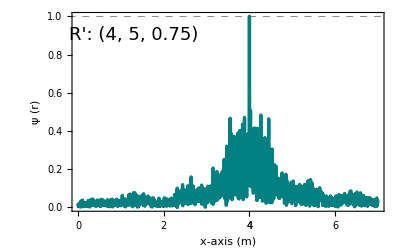

```mathematica
crosSecPlot1=radiationAlongX[xStr,yStr,zStr,fullExcitationPattern,radiationWithXY1Max,Dis1,dis1,S1,T1,U1,V1,λe,"Chap5Fig6b.pdf"]
```

Figure 6e : beam pattern along y axis at R = (4, 5, 0.75)

Max relative intensity along y axis :152.563

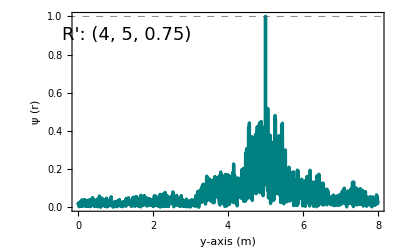

```mathematica
crosSecPlot2=radiationAlongY[xStr,yStr,zStr,fullExcitationPattern,radiationWithXY1Max,Dis1,dis1,S1,T1,U1,V1,λe,"Chap5Fig6e.pdf"]
```

Radiation pattern of M = 5x6 optical cluster arrangement . each Optical cluster  is consist of N = (5 x5) nano radiating elements . distance between clusters is D = 1 m and distance between nano elements d = 780nm

```mathematica
S1=5;
T1=6;
U11=5;
V11=5;
```

```mathematica
Dis1=1;
dis1=λd/2;
λe1=Dis1*2;
```

```mathematica
radiationWithXY11= Abs[Total[planar[λd,λe1,x,y,zStr,Dis1,dis1,S1,T1,U11,V11,xMiddle,yMiddle,xStr,yStr,zStr],2]];
datapair11=ParallelTable[radiationWithXY11,{x,0,xLength,0.1},{y,0,yLength,0.1}];
radiationWithXY11Max=Max[datapair11]
```

238.379

```mathematica
fullExcitationPattern1=ConstantArray[1,{S1,T1}]
```

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}}

Figure 6b: beam pattern along x axis at R = (4, 5, 0.75)

Max relative intensity along x axis :238.379

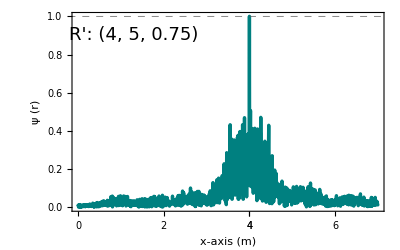

```mathematica
crosSecPlot11=radiationAlongX[xStr,yStr,zStr,fullExcitationPattern1,radiationWithXY11Max,Dis1,dis1,S1,T1,U11,V11,λe1,"Chap5Fig6b1.pdf"]
```

Figure 6e: beam pattern along y axis at R = (4, 5, 0.75)

Max relative intensity along y axis :238.379

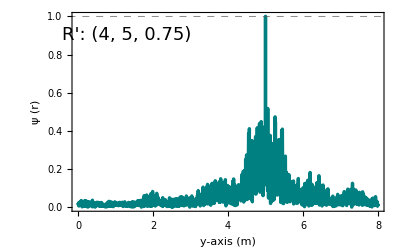

```mathematica
crosSecPlot12=radiationAlongY[xStr,yStr,zStr,fullExcitationPattern1,radiationWithXY11Max,Dis1,dis1,S1,T1,U11,V11,λe1,"Chap5Fig6e1.pdf"]
```

Radiation pattern of M = 7x8 optical cluster arrangement . each Optical cluster  is consist of N = (4 x4) nano radiating elements . distance between clusters is D = 0.75 m and distance between nano elements d = 780nm

```mathematica
S2=7;
T2=8;
U2=4;
V2=4;
```

```mathematica
Dis2=0.75;
dis2=λd/2;
λe2=Dis2*2;
```

```mathematica
radiationWithXY2= Abs[Total[planar[λd,λe2,x,y,zStr,Dis2,dis2,S2,T2,U2,V2,xMiddle,yMiddle,xStr,yStr,zStr],2]];
datapair2=ParallelTable[radiationWithXY2,{x,0,xLength,0.1},{y,0,yLength,0.1}];
radiationWithXY2Max=Max[datapair2]
```

281.8

```mathematica
radiationWithYZ2= Abs[Total[planar[λd,λe2,xStr,y,z,Dis2,dis2,S2,T2,U2,V2,xMiddle,yMiddle,xStr,yStr,zStr],2]];
```

```mathematica
fullExcitationPattern2=ConstantArray[1,{S2,T2}]
```

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

Figure 6c: beam pattern along x axis at R = (4, 5, 0.75)

Max relative intensity along x axis :281.8

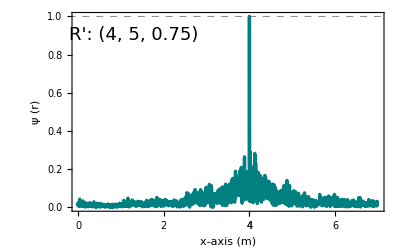

```mathematica
crosSecPlot3=radiationAlongX[xStr,yStr,zStr,fullExcitationPattern2,radiationWithXY2Max,Dis2,dis2,S2,T2,U2,V2,λe2,"Chap5Fig6c.pdf"]
```

Figure 6f: beam pattern along y axis at R = (4, 5, 0.75)

Max relative intensity along y axis :281.8

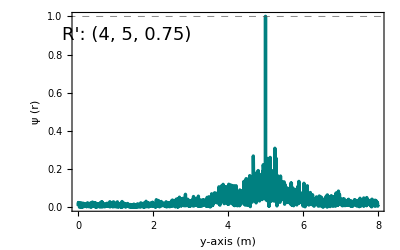

```mathematica
crosSecPlot4=radiationAlongY[xStr,yStr,zStr,fullExcitationPattern2,radiationWithXY2Max,Dis2,dis2,S2,T2,U2,V2,λe2,"Chap5Fig6f.pdf"]
```

Radiation pattern of M = 3x4 optical cluster arrangement . each Optical cluster  is consist of N = (4 x4) nano radiating elements . distance between clusters is D = 2 m and distance between nano elements d = 780nm

```mathematica
S3=3;
T3=4;
U3=4;
V3=4;
```

```mathematica
Dis3=2;
dis3=λd/2;
λe3=Dis3*2;
```

```mathematica
radiationWithXY3= Abs[Total[planar[λd,λe3,x,y,zStr,Dis3,dis3,S3,T3,U3,V3,xMiddle,yMiddle,xStr,yStr,zStr],2]];
datapair3=ParallelTable[radiationWithXY3,{x,0,xLength,0.1},{y,0,yLength,0.1}];
radiationWithXY3Max=Max[datapair3]
```

55.6347

```mathematica
fullExcitationPattern3=ConstantArray[1,{S3,T3}]
```

{{1,1,1,1},{1,1,1,1},{1,1,1,1}}

Figure 6a: beam pattern along x axis at R = (4, 5, 0.75)

Max relative intensity along x axis :55.6347

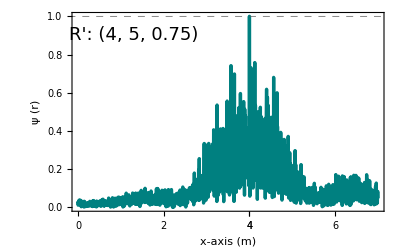

```mathematica
crosSecPlot5=radiationAlongX[xStr,yStr,zStr,fullExcitationPattern3,radiationWithXY3Max,Dis3,dis3,S3,T3,U3,V3,λe3,"Chap5Fig6a.pdf"]
```

Figure 6d: beam pattern along y axis at R = (4, 5, 0.75)

Max relative intensity along y axis :55.6347

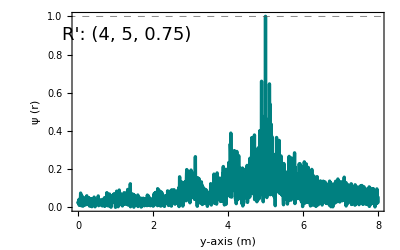

```mathematica
crosSecPlot6=radiationAlongY[xStr,yStr,zStr,fullExcitationPattern3,radiationWithXY3Max,Dis3,dis3,S3,T3,U3,V3,λe2,"Chap5Fig6d.pdf"]
```

#### Finding effective radiation pattern using ACO algorithm .

We consider same Room with similar dimensions . same array with cluster count m=(5 x6) and  n=(4X4) and the same steer point as below .

```mathematica
sCount=5;
tCount=6;
uCount=4;
vCount=4;
xSteer=4;
ySteer=5;
zSteer=0.75;
```

```mathematica
radiation=planar[λd,λe,x,y,zStr,Dis1,dis1,sCount,tCount,uCount,vCount,xMiddle,yMiddle,xSteer,ySteer,zSteer];
radTotal=Abs[Total[radiation,2]];
datapair=ParallelTable[radTotal,{x,0,xLength,0.1},{y,0,yLength,0.1}];
radiationMax=Max[datapair]
```

152.563

Now we initiate the parameters which required for algorithm

```mathematica
iterationsPlnr=30;(*No of Iterations*)
(*offCountPlnr=15;*)(*No off antenna count*)
numAntsPlnr=10;(*No of ants consider for the colony*)
pheromoneDecayPlnr=0.5;(*Phermone decaying constant. This is the best value for array thinning problem*)
alphaPlnr=1;(*Pheromone wieght*)
betaPlnr=1;(*heuristic criteria wieght*)
desiredSLLPlanar=-20;
```

```mathematica
findChebyshevCoefficients[n_,sll_]:=Module[{sllAtt,chebyshevCoefficients,ModifiedChebyshevCoefficients},
sllAtt=sll/20;
chebyshevCoefficients=ResourceFunction["DiscreteDolphChebyshevWindow"][n,sllAtt];
ModifiedChebyshevCoefficients=chebyshevCoefficients/Max[chebyshevCoefficients];
ModifiedChebyshevCoefficients
]
```

```mathematica
findChebyPlanar[n_,m_,sll_]:=Module[{wRow,wCol,wPlanar},
wRow=findChebyshevCoefficients[n,sll];
wCol=findChebyshevCoefficients[m,sll];
wPlanar=Outer[Times,wRow,wCol];
wPlanar
]
```

```mathematica
decisionPlanar[localAnt_,localPheromones_,offCount_]:=Module[{r,modifiedη,antDuplicate,probability},
modifiedη=planarη;
antDuplicate=localAnt;
While[Count[antDuplicate,0,{2}]<offCount,
{
probability=(localPheromones^alphaPlnr)*(modifiedη^betaPlnr);
probability=probability/Total[probability,2];
r=RandomReal[];
total=0;
Table[total+=probability[[i]][[j]]; 
If[total>=r && antDuplicate[[i]][[j]]==1, 
{antDuplicate[[i]][[j]]=0;
(*Print[probability];
Print[antDuplicate];*);
Goto[end];},]
,{i,1,Length[probability]},{j,1,Length[probability[[1]]]}
];
Label[end];
modifiedη=ReplacePart[modifiedη,Thread[Position[antDuplicate,0]->0]];
(*Print[modifiedη];*)
}
];
antDuplicate
]
```

```mathematica
decidePlanarNodeThinning[localPheromones_,n_,m_,off_]:=Module[{antColony},
antColony=Table[ants=ConstantArray[1,{sCount,tCount}],{ants,numAntsPlnr}];
antColony=Table[decisionPlanar[ant,localPheromones,off],{ant,antColony}];
antColony
]
```

```mathematica
objectiveFunPlanar[localAnt_]:=Module[{rad,radiationSLL},
(*Print[localAnt];*)
rad=Abs[Total[radiation*localAnt,2]];
radiationSLL=findPlanarSLL[{xStr,yStr,zStr},localAnt,Dis1,dis1,sCount,tCount,uCount,vCount,λe][[1]];
Return[desiredSLLPlanar-radiationSLL];
]
```

```mathematica
updatePheromone[pheromone_,localResult_]:=Module[{delta,ant,sol},
delta=0;
ant=localResult[[1]][[1]];
sol=localResult[[1]][[2]];
If[ant[[ pheromone[[1]]]][[pheromone[[2]]]]==0,delta=(10/Abs[sol]),];
delta
]
```

```mathematica
findBestAnt[list_,func_]:=list[[Ordering[func/@list,-1]]]
```

```mathematica
acoAlgorithm[fullRadiation_,off_]:=Module[{attempts,bestAntPlanarList,currentResultPlanar,equalResult,oldResultPlanar,pheromonesPlanar,planarη,itrCount,eqResultCount,antColonyPlanar,antSolPlanar,itrBestAntIndex,itrBestAnt},
attempts=0;
Label[begin];
bestAntPlanarList={};
currentResultPlanar={};
oldResultPlanar={};
equalResult=0;
pheromonesPlanar=ConstantArray[1,{sCount,tCount}];
planarη=findChebyPlanar[sCount,tCount,desiredSLLPlanar];
itrCount=Ceiling[iterationsPlnr/2];
eqResultCount=Ceiling[iterationsPlnr/4];
Do[
(*Print["Work start here"];*)
antColonyPlanar=decidePlanarNodeThinning[pheromonesPlanar,sCount,tCount,off];
(*Print["111111111111111111111111111111111"];
Print[antColonyPlanar];*)
antSolPlanar=Table[objectiveFunPlanar[ant],{ant,antColonyPlanar}];
(*Print["222222222222222222222222222222222"];
Print[antSolPlanar];*)
itrBestAntIndex=Ordering[antSolPlanar,-1][[1]];
itrBestAnt=antColonyPlanar[[itrBestAntIndex]];
(*Print["33333333333333333333333333333333333"];
Print[itrBestAnt];*)
AppendTo[bestAntPlanarList,{itrBestAnt,antSolPlanar[[itrBestAntIndex]]}];
(*Print["444444444444444444444444444444444444"];
Print[bestAntPlanarList];*)
oldResultPlanar=currentResultPlanar;
currentResultPlanar=findBestAnt[bestAntPlanarList,Last];
(*Print["555555555555555555555555555555555555"];
Print[currentResultPlanar];*)
If[currentResultPlanar==oldResultPlanar,equalResult++,equalResult=0];
(*Print["6666666666666666666666666666666666"];
Print[equalResult];*)
If[equalResult>eqResultCount && iter<itrCount,{pheromonesPlanar=ConstantArray[1,{sCount,tCount}];
equalResult=0;
},
{pheromonesPlanar=(1-pheromoneDecayPlnr)*pheromonesPlanar;
(*Table[updatePheromone[{i,j},bestAntPlanarList],{i,Length[pheromonesPlanar]},{j,Length[pheromonesPlanar[[1]]]}]*)
pheromonesPlanar+=Table[updatePheromone[{i,j},currentResultPlanar],{i,Length[pheromonesPlanar]},{j,Length[pheromonesPlanar[[1]]]}];
}
];
(*Print[pheromonesPlanar];*)
,{iter,iterationsPlnr}
];
If[currentResultPlanar[[1]][[2]]<(desiredSLLPlanar-(-3)) && attempts<5,
{
(*Print["Oh god !!!! answer not good"];*)
attempts++;
Goto[begin];
},
];
currentResultPlanar
]
```

Generate excitation pattern for different inactive cluster counts.

```mathematica
configCal[radiation_,sCount_,tCount_]:=Module[{i,configList,onoffConfig},
configList={};
For[i=1,i<25,i++,
{onoffConfig=acoAlgorithm[radiation,i];
	Print[onoffConfig[[1]][[1]]];
	AppendTo[configList,onoffConfig[[1]][[1]]];
}
];
configList
]
```

```mathematica
configList=configCal[radiation,sCount,tCount];
```

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1}}

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,0,1,1},{1,1,1,0,1,1},{1,1,1,1,1,1}}

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,0,0,1},{1,1,1,0,1,1},{1,1,1,1,1,1}}

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,1,1,0,0,0},{1,1,1,1,1,1}}

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,1,0,0,0,1},{1,1,1,1,0,1}}

{{1,1,1,1,1,1},{1,1,1,0,1,1},{1,1,1,1,1,1},{0,1,1,0,0,0},{1,1,1,1,0,1}}

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,1,0,0,1,1},{1,1,1,0,0,1}}

{{1,1,1,1,1,1},{1,1,0,0,1,1},{1,1,1,1,1,1},{0,1,1,0,0,0},{1,1,0,0,1,1}}

{{1,1,1,1,1,1},{1,0,1,1,1,0},{1,1,0,1,1,1},{1,0,1,0,0,0},{1,1,1,1,0,0}}

{{1,1,1,1,1,1},{1,1,1,0,0,0},{0,1,0,1,1,1},{1,1,1,0,0,0},{0,1,1,1,1,0}}

{{1,1,1,1,1,1},{1,1,1,0,0,0},{1,1,1,1,0,1},{0,0,0,0,0,1},{1,1,1,1,0,0}}

{{1,1,1,1,1,1},{1,0,1,0,0,1},{1,1,0,0,0,1},{1,1,1,1,0,0},{0,0,1,0,1,0}}

{{1,1,1,1,1,1},{1,1,1,1,1,0},{0,1,1,0,1,0},{0,0,0,0,0,0},{1,1,1,0,0,0}}

{{1,1,1,1,1,1},{1,1,1,0,0,0},{1,1,0,1,0,0},{0,0,0,0,0,1},{1,0,0,0,1,1}}

{{0,0,1,1,0,0},{1,1,0,0,0,0},{1,0,0,1,0,1},{1,1,0,0,0,1},{1,1,0,1,1,1}}

{{1,0,0,0,0,1},{1,0,0,0,1,0},{1,1,0,1,0,0},{1,1,0,0,0,0},{1,1,1,1,0,1}}

{{1,0,1,1,1,0},{1,0,1,0,1,0},{0,0,1,0,1,0},{0,0,0,1,0,0},{1,0,1,1,0,0}}

{{1,1,1,1,0,1},{0,0,1,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{1,1,1,0,1,0}}

{{1,1,1,1,0,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{1,1,1,1,0,0},{1,0,1,0,0,0}}

{{1,1,1,1,1,1},{0,0,1,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,0,0,0,0}}

{{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,0,1},{1,0,0,0,0,0}}

{{1,0,1,1,1,1},{1,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,0,0,0,0,0}}

{{1,1,0,1,0,0},{1,0,1,0,0,0},{0,0,0,0,0,0},{0,0,1,1,0,0},{0,0,0,0,0,0}}

{{1,0,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,0,0}}

```mathematica
configList={{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},
{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,0,1,1},{1,1,1,0,1,1},{1,1,1,1,1,1}},
{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,0,0,1},{1,1,1,0,1,1},{1,1,1,1,1,1}},
{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,1,1,0,0,0},{1,1,1,1,1,1}},
{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,1,0,0,0,1},{1,1,1,1,0,1}},
{{1,1,1,1,1,1},{1,1,1,0,1,1},{1,1,1,1,1,1},{0,1,1,0,0,0},{1,1,1,1,0,1}},
{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,1,0,0,1,1},{1,1,1,0,0,1}},
{{1,1,1,1,1,1},{1,1,0,0,1,1},{1,1,1,1,1,1},{0,1,1,0,0,0},{1,1,0,0,1,1}},
{{1,1,1,1,1,1},{1,0,1,1,1,0},{1,1,0,1,1,1},{1,0,1,0,0,0},{1,1,1,1,0,0}},
{{1,1,1,1,1,1},{1,1,1,0,0,0},{0,1,0,1,1,1},{1,1,1,0,0,0},{0,1,1,1,1,0}},
{{1,1,1,1,1,1},{1,1,1,0,0,0},{1,1,1,1,0,1},{0,0,0,0,0,1},{1,1,1,1,0,0}},
{{1,1,1,1,1,1},{1,0,1,0,0,1},{1,1,0,0,0,1},{1,1,1,1,0,0},{0,0,1,0,1,0}},
{{1,1,1,1,1,1},{1,1,1,1,1,0},{0,1,1,0,1,0},{0,0,0,0,0,0},{1,1,1,0,0,0}},
{{1,1,1,1,1,1},{1,1,1,0,0,0},{1,1,0,1,0,0},{0,0,0,0,0,1},{1,0,0,0,1,1}},
{{0,0,1,1,0,0},{1,1,0,0,0,0},{1,0,0,1,0,1},{1,1,0,0,0,1},{1,1,0,1,1,1}},
{{1,0,0,0,0,1},{1,0,0,0,1,0},{1,1,0,1,0,0},{1,1,0,0,0,0},{1,1,1,1,0,1}},
{{1,0,1,1,1,0},{1,0,1,0,1,0},{0,0,1,0,1,0},{0,0,0,1,0,0},{1,0,1,1,0,0}},
{{1,1,1,1,0,1},{0,0,1,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{1,1,1,0,1,0}},
{{1,1,1,1,0,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{1,1,1,1,0,0},{1,0,1,0,0,0}},
{{1,1,1,1,1,1},{0,0,1,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,0,0,0,0}},
{{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,0,1},{1,0,0,0,0,0}},
{{1,0,1,1,1,1},{1,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,0,0,0,0,0}},
{{1,1,0,1,0,0},{1,0,1,0,0,0},{0,0,0,0,0,0},{0,0,1,1,0,0},{0,0,0,0,0,0}},
{{1,0,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,0,0}}};
```

Fig7: Analyze the resulting excitation pattern for different inactive clusters values

Analyze the resulting excitation pattern for M' = 5

```mathematica
configList[[5,All]]
```

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,1,0,0,0,1},{1,1,1,1,0,1}}

```mathematica
radiation5Inactive= Abs[Total[planar[λd,λe,x,y,zStr,Dis1,dis1,sCount,tCount,uCount,vCount,xMiddle,yMiddle,xStr,yStr,zStr]*configList[[5,All]],2]];
datapair5Inactive=ParallelTable[radiation5Inactive,{x,0,xLength,0.1},{y,0,yLength,0.1}];
radiation5InactiveMax=Max[datapair5Inactive]
```

123.54

```mathematica
plotDataPair5Inactive=Flatten[ParallelTable[{x,y,20*Log[10,radiation5Inactive/radiation5InactiveMax]},{x,0,xLength+1,0.1},{y,0,yLength+1,0.1}],1];
```

```mathematica
normalizedPlot5Inactive=plotPlanarRadiationXY[plotDataPair5Inactive,20];
```

```mathematica
plotAnnotations5Inactive=Graphics[{EdgeForm[{Dashed,RGBColor[0.6,0.6,0.6]}],(*Outline style for the rectangle*)FaceForm[None],Rectangle[{xStr-0.5,yStr-0.5},{xStr+0.5,yStr+0.5}]}];
mainPlotWithAnnotations5Inactive=Show[normalizedPlot5Inactive,plotAnnotations5Inactive];
```

```mathematica
zoomDataPair5Inactive=Flatten[ParallelTable[{x,y,20*Log[10,radiation5Inactive/radiation5InactiveMax]},{x,xStr-0.5,xStr+0.5,0.1},{y,yStr-0.5,yStr+0.5,0.1}],1];
```

```mathematica
zoomplot5Inactive=zoomplotPlanarRadiationXY[zoomDataPair5Inactive];
```

Fig.7a Beam focusing pattern for M' = 5

```mathematica
Show[mainPlotWithAnnotations5Inactive,Epilog->{Inset[zoomplot5Inactive,Scaled[{0.23,0.02}],(*position inside main plot*)Bottom,Scaled[{0.4,0.5}]    (*size of inset plot*)]}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig7a.pdf"}],Rasterize[Show[mainPlotWithAnnotations5Inactive,Epilog->{Inset[zoomplot5Inactive,Scaled[{0.25,0.05}],Bottom,Scaled[{0.4,0.5}]]}],"Image",ImageResolution->300]];
```

```mathematica
psllResult5Inactive=findPlanarSLL[{xStr,yStr,zStr},configList[[5,All]],Dis1,dis1,sCount,tCount,uCount,vCount,λe];
```

```mathematica
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{psllResult5Inactive[[1]],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],psllResult5Inactive[[2]]}},Frame->All]
```

PSLL Value   : | -7.5284 dB
PSLL Location : | {4.4,5.,0.75}

```mathematica
beamwidth5Inactive=effectiveBeamArea[radiation5Inactive,{xStr,yStr,zStr},0.01,1*10^-6];
```

123.54

{{3.99793,0.713963},{3.99928,0.788464},{4.,1.},{4.00073,0.788606}}

{3.99793,4.00073}

123.54

{{5.,1.}}

{5.,5.}

```mathematica
Grid[{{Style["Focal spot Area :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{NumberForm[beamwidth5Inactive[[1]]*1000,{5,3}]," × ",NumberForm[beamwidth5Inactive[[2]]*1000,{5,3}]," mm^2"}]}},Frame->All,Alignment->Center,Spacings->{2,2}]
```

Focal spot Area : | 2.793 × 0.000 mm^2

Analyze the resulting excitation pattern for M’ = 10

```mathematica
configList[[10,All]]
```

{{1,1,1,1,1,1},{1,1,1,0,0,0},{0,1,0,1,1,1},{1,1,1,0,0,0},{0,1,1,1,1,0}}

```mathematica
radiation10Inactive= Abs[Total[planar[λd,λe,x,y,zStr,Dis1,dis1,sCount,tCount,uCount,vCount,xMiddle,yMiddle,xStr,yStr,zStr]*configList[[10,All]],2]];
datapair10Inactive=ParallelTable[radiation10Inactive,{x,0,xLength,0.1},{y,0,yLength,0.1}];
radiation10InactiveMax=Max[datapair10Inactive]
```

97.9383

```mathematica
plotDataPair10Inactive=Flatten[ParallelTable[{x,y,20*Log[10,radiation10Inactive/radiation10InactiveMax]},{x,0,xLength,0.1},{y,0,yLength,0.1}],1];
```

```mathematica
normalizedPlot10Inactive=plotPlanarRadiationXY[plotDataPair10Inactive,20];
```

```mathematica
plotAnnotations10Inactive=Graphics[{EdgeForm[{Dashed,RGBColor[0.6,0.6,0.6]}],(*Outline style for the rectangle*)FaceForm[None],Rectangle[{xStr-0.5,yStr-0.5},{xStr+0.5,yStr+0.5}]}];
mainPlotWithAnnotations10Inactive=Show[normalizedPlot10Inactive,plotAnnotations10Inactive];
```

```mathematica
zoomDataPair10Inactive=Flatten[ParallelTable[{x,y,20*Log[10,radiation10Inactive/radiation10InactiveMax]},{x,xStr-0.5,xStr+0.5,0.1},{y,yStr-0.5,yStr+0.5,0.1}],1];
```

```mathematica
zoomplot10Inactive=zoomplotPlanarRadiationXY[zoomDataPair10Inactive];
```

Fig.7b Beam focusing pattern for M' = 10

```mathematica
Show[mainPlotWithAnnotations10Inactive,Epilog->{Inset[zoomplot10Inactive,Scaled[{0.23,0.02}],(*position inside main plot*)Bottom,Scaled[{0.4,0.5}]    (*size of inset plot*)]}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig7b.pdf"}],Rasterize[Show[mainPlotWithAnnotations10Inactive,Epilog->{Inset[zoomplot10Inactive,Scaled[{0.25,0.05}],Bottom,Scaled[{0.4,0.5}]]}],"Image",ImageResolution->300]];
```

```mathematica
psllResult10Inactive=findPlanarSLL[{xStr,yStr,zStr},configList[[10,All]],Dis1,dis1,sCount,tCount,uCount,vCount,λe];
```

```mathematica
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{psllResult10Inactive[[1]],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],psllResult10Inactive[[2]]}},Frame->All]
```

PSLL Value   : | -7.80877 dB
PSLL Location : | {3.65,4.65,0.75}

```mathematica
beamwidth10Inactive=effectiveBeamArea[radiation10Inactive,{xStr,yStr,zStr},0.01,1*10^-6];
```

97.9383

{{3.99062,0.714685},{3.99096,0.716576},{3.99464,0.761424},{3.99491,0.723415},{3.99793,0.810671},{3.99798,0.716362},{3.99855,0.740848},{3.99928,0.752195},{4.,1.},{4.00073,0.758273}}

{3.99062,4.00073}

97.9383

{{4.99291,0.70791},{5.,1.}}

{4.99291,5.}

```mathematica
Grid[{{Style["Focal spot Area :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{NumberForm[beamwidth10Inactive[[1]]*1000,{5,3}]," × ",NumberForm[beamwidth10Inactive[[2]]*1000,{5,3}]," mm^2"}]}},Frame->All,Alignment->Center,Spacings->{2,2}]
```

Focal spot Area : | 10.103 × 7.086 mm^2

Analyze the resulting excitation pattern for M’ = 15

```mathematica
configList[[15,All]]
```

{{0,0,1,1,0,0},{1,1,0,0,0,0},{1,0,0,1,0,1},{1,1,0,0,0,1},{1,1,0,1,1,1}}

```mathematica
radiation15Inactive= Abs[Total[planar[λd,λe,x,y,zStr,Dis1,dis1,sCount,tCount,uCount,vCount,xMiddle,yMiddle,xStr,yStr,zStr]*configList[[15,All]],2]];
datapair15Inactive=ParallelTable[radiation15Inactive,{x,0,xLength,0.1},{y,0,yLength,0.1}];
radiation15InactiveMax=Max[datapair15Inactive]
```

72.5462

```mathematica
plotDataPair15Inactive=Flatten[ParallelTable[{x,y,20*Log[10,radiation15Inactive/radiation15InactiveMax]},{x,0,xLength,0.1},{y,0,yLength,0.1}],1];
```

```mathematica
normalizedPlot15Inactive=plotPlanarRadiationXY[plotDataPair15Inactive,20];
```

```mathematica
plotAnnotations15Inactive=Graphics[{EdgeForm[{Dashed,RGBColor[0.6,0.6,0.6]}],(*Outline style for the rectangle*)FaceForm[None],Rectangle[{xStr-0.5,yStr-0.5},{xStr+0.5,yStr+0.5}]}];
mainPlotWithAnnotations15Inactive=Show[normalizedPlot15Inactive,plotAnnotations15Inactive];
```

```mathematica
zoomDataPair15Inactive=Flatten[ParallelTable[{x,y,20*Log[10,radiation15Inactive/radiation15InactiveMax]},{x,xStr-0.5,xStr+0.5,0.1},{y,yStr-0.5,yStr+0.5,0.1}],1];
```

```mathematica
zoomplot15Inactive=zoomplotPlanarRadiationXY[zoomDataPair15Inactive];
```

Fig.7c Beam focusing pattern for M' = 15

```mathematica
Show[mainPlotWithAnnotations15Inactive,Epilog->{Inset[zoomplot15Inactive,Scaled[{0.23,0.02}],(*position inside main plot*)Bottom,Scaled[{0.4,0.5}]    (*size of inset plot*)]}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig7c.pdf"}],Rasterize[Show[mainPlotWithAnnotations15Inactive,Epilog->{Inset[zoomplot15Inactive,Scaled[{0.25,0.05}],Bottom,Scaled[{0.4,0.5}]]}],"Image",ImageResolution->300]];
```

```mathematica
psllResult15Inactive=findPlanarSLL[{xStr,yStr,zStr},configList[[15,All]],Dis1,dis1,sCount,tCount,uCount,vCount,λe];
```

```mathematica
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{psllResult15Inactive[[1]],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],psllResult15Inactive[[2]]}},Frame->All]
```

PSLL Value   : | -6.92338 dB
PSLL Location : | {4.45,5.,0.75}

```mathematica
beamwidth15Inactive=effectiveBeamArea[radiation15Inactive,{xStr,yStr,zStr},0.01,1*10^-6];
```

72.5462

{{3.99198,0.801401},{3.9923,0.743081},{3.99264,0.72136},{3.99491,0.822346},{3.99798,0.724665},{3.99855,0.801278},{3.9987,0.720311},{3.99928,0.811434},{3.99943,0.780079},{4.,1.},{4.00058,0.777912},{4.00073,0.822866},{4.0013,0.753288},{4.00165,0.710589},{4.00509,0.720888},{4.00514,0.733198},{4.008,0.745777},{4.00928,0.754152}}

{3.99198,4.00928}

72.5462

{{4.99004,0.739724},{4.99009,0.774786},{4.99013,0.709547},{4.99068,0.74382},{4.99094,0.71287},{4.99104,0.768788},{4.9915,0.74257},{4.99218,0.716458},{4.99225,0.709962},{4.99236,0.721611},{4.99251,0.788064},{4.99275,0.71414},{4.99403,0.751735},{4.99409,0.769956},{4.99442,0.721622},{4.99481,0.772804},{4.99486,0.738177},{4.99491,0.789898},{4.99528,0.718831},{4.99641,0.783463},{4.99648,0.719367},{4.99662,0.79006},{4.99726,0.729761},{4.99773,0.776608},{4.99855,0.780514},{4.99928,0.744111},{4.99932,0.769731},{4.99986,0.709637},{5.,1.},{5.00014,0.711058},{5.00068,0.736245},{5.00135,0.74289},{5.00139,0.842187},{5.00153,0.720389},{5.00156,0.719342},{5.00161,0.747596},{5.0017,0.720895},{5.00202,0.783257},{5.00228,0.71476},{5.00264,0.818931},{5.00274,0.741862},{5.00398,0.73128},{5.00424,0.722603},{5.00451,0.717156},{5.00474,0.780576},{5.00496,0.720542},{5.00509,0.742128},{5.00577,0.817379},{5.00602,0.723847},{5.00634,0.775327},{5.00659,0.718567},{5.00673,0.710757},{5.00698,0.730793},{5.00709,0.7185},{5.00744,0.751064},{5.0077,0.714241},{5.00806,0.714675},{5.00884,0.720209},{5.00933,0.804744},{5.0099,0.710588}}

{4.99004,5.0099}

```mathematica
Grid[{{Style["Focal spot Area :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{NumberForm[beamwidth15Inactive[[1]]*1000,{5,3}]," × ",NumberForm[beamwidth15Inactive[[2]]*1000,{5,3}]," mm^2"}]}},Frame->All,Alignment->Center,Spacings->{2,2}]
```

Focal spot Area : | 17.302 × 19.858 mm^2

Analyze the resulting excitation pattern for M’ = 20

```mathematica
configList[[20,All]]
```

{{1,1,1,1,1,1},{0,0,1,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,0,0,0,0}}

```mathematica
radiation20Inactive= Abs[Total[planar[λd,λe,x,y,zStr,Dis1,dis1,sCount,tCount,uCount,vCount,xMiddle,yMiddle,xStr,yStr,zStr]*configList[[20,All]],2]];
datapair20Inactive=ParallelTable[radiation20Inactive,{x,0,xLength,0.1},{y,0,yLength,0.1}];
radiation20InactiveMax=Max[datapair20Inactive]
```

44.1684

```mathematica
plotDataPair20Inactive=Flatten[ParallelTable[{x,y,20*Log[10,radiation20Inactive/radiation20InactiveMax]},{x,0,xLength,0.1},{y,0,yLength,0.1}],1];
```

```mathematica
normalizedPlot20Inactive=plotPlanarRadiationXY[plotDataPair20Inactive,20];
```

```mathematica
plotAnnotations20Inactive=Graphics[{EdgeForm[{Dashed,RGBColor[0.6,0.6,0.6]}],(*Outline style for the rectangle*)FaceForm[None],Rectangle[{xStr-0.5,yStr-0.5},{xStr+0.5,yStr+0.5}]}];
mainPlotWithAnnotations20Inactive=Show[normalizedPlot20Inactive,plotAnnotations20Inactive];
```

```mathematica
zoomDataPair20Inactive=Flatten[ParallelTable[{x,y,20*Log[10,radiation20Inactive/radiation20InactiveMax]},{x,xStr-0.5,xStr+0.5,0.1},{y,yStr-0.5,yStr+0.5,0.1}],1];
```

```mathematica
zoomplot20Inactive=zoomplotPlanarRadiationXY[zoomDataPair20Inactive];
```

Fig.7d Beam focusing pattern for M' = 20

```mathematica
Show[mainPlotWithAnnotations20Inactive,Epilog->{Inset[zoomplot20Inactive,Scaled[{0.23,0.02}],(*position inside main plot*)Bottom,Scaled[{0.4,0.5}]    (*size of inset plot*)]}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig7d.pdf"}],Rasterize[Show[mainPlotWithAnnotations20Inactive,Epilog->{Inset[zoomplot20Inactive,Scaled[{0.25,0.05}],Bottom,Scaled[{0.4,0.5}]]}],"Image",ImageResolution->300]];
```

```mathematica
psllResult20Inactive=findPlanarSLL[{xStr,yStr,zStr},configList[[20,All]],Dis1,dis1,sCount,tCount,uCount,vCount,λe];
```

```mathematica
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{psllResult20Inactive[[1]],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],psllResult20Inactive[[2]]}},Frame->All]
```

PSLL Value   : | -5.3456 dB
PSLL Location : | {3.8,5.,0.75}

```mathematica
beamwidth20Inactive=effectiveBeamArea[radiation20Inactive,{xStr,yStr,zStr},0.01,1*10^-6];
```

44.1684

{{3.99005,0.739377},{3.99011,0.9041},{3.99016,0.784348},{3.99016,0.749643},{3.9902,0.713962},{3.99022,0.758575},{3.99027,0.787546},{3.99032,0.764566},{3.99055,0.815293},{3.99057,0.74625},{3.99066,0.824907},{3.9908,0.733013},{3.99091,0.882339},{3.99096,0.807707},{3.99096,0.732646},{3.99102,0.826542},{3.99107,0.810414},{3.99108,0.709558},{3.99112,0.775859},{3.99121,0.736024},{3.99123,0.721136},{3.99127,0.751329},{3.99132,0.813429},{3.99132,0.752596},{3.99137,0.730159},{3.99137,0.716743},{3.99143,0.747176},{3.99148,0.755012},{3.99148,0.712782},{3.99157,0.821453},{3.99162,0.759916},{3.99168,0.807546},{3.99173,0.787466},{3.99173,0.823851},{3.99176,0.722841},{3.99184,0.725798},{3.99185,0.730218},{3.99187,0.78617},{3.9919,0.737757},{3.99193,0.763946},{3.99198,0.750665},{3.99201,0.745789},{3.99209,0.779045},{3.99212,0.783406},{3.99212,0.763789},{3.99221,0.7154},{3.99223,0.794096},{3.99226,0.731218},{3.99229,0.731523},{3.99234,0.720703},{3.99237,0.83745},{3.99242,0.740273},{3.99248,0.880703},{3.99254,0.848397},{3.99259,0.763033},{3.99265,0.808403},{3.99273,0.801622},{3.99278,0.743478},{3.99284,0.807472},{3.99289,0.718709},{3.9929,0.829766},{3.9929,0.730266},{3.99301,0.744534},{3.99303,0.709914},{3.99314,0.738571},{3.99315,0.828114},{3.99319,0.840978},{3.99325,0.720023},{3.99326,0.782918},{3.99331,0.850486},{3.99339,0.713802},{3.99344,0.770542},{3.9935,0.770211},{3.99351,0.771219},{3.99355,0.91954},{3.99356,0.738358},{3.99361,0.752255},{3.99367,0.851279},{3.99369,0.747381},{3.9938,0.717926},{3.9938,0.899007},{3.99386,0.817145},{3.99391,0.777623},{3.99392,0.908159},{3.99397,0.709702},{3.99397,0.893785},{3.99403,0.744143},{3.99405,0.76605},{3.99408,0.79324},{3.99416,0.90081},{3.99422,0.847051},{3.99422,0.763177},{3.99428,0.845351},{3.99433,0.87458},{3.99433,0.747559},{3.99441,0.715125},{3.99444,0.737453},{3.99447,0.786296},{3.99452,0.720267},{3.99453,0.740965},{3.99458,0.907241},{3.99463,0.766266},{3.99464,0.73203},{3.99469,0.798726},{3.99474,0.723506},{3.99483,0.762982},{3.99494,0.781467},{3.99499,0.775168},{3.99513,0.776259},{3.99524,0.859476},{3.9953,0.762662},{3.99535,0.781025},{3.99541,0.756005},{3.99549,0.742802},{3.99554,0.718971},{3.99555,0.716514},{3.9956,0.75229},{3.99566,0.761647},{3.99566,0.781971},{3.99579,0.734315},{3.99591,0.851335},{3.99591,0.753185},{3.99596,0.78954},{3.99602,0.77061},{3.99602,0.766546},{3.99607,0.792384},{3.99615,0.78064},{3.99621,0.737543},{3.99627,0.808923},{3.99632,0.761438},{3.99632,0.838169},{3.99634,0.748596},{3.99644,0.707257},{3.99652,0.748904},{3.99657,0.869417},{3.99662,0.718454},{3.99663,0.719367},{3.99668,0.825901},{3.99673,0.7212},{3.99682,0.710344},{3.99687,0.790657},{3.99693,0.710262},{3.99698,0.811059},{3.99701,0.763456},{3.99712,0.751189},{3.9972,0.710069},{3.99721,0.78543},{3.99723,0.742445},{3.99726,0.792661},{3.99737,0.816225},{3.99746,0.850257},{3.99748,0.720802},{3.99751,0.782603},{3.99751,0.793776},{3.99757,0.795398},{3.99762,0.821429},{3.99763,0.806667},{3.99767,0.777276},{3.99771,0.806028},{3.99776,0.736277},{3.99782,0.813236},{3.99787,0.749695},{3.99788,0.823506},{3.9979,0.733308},{3.99792,0.731333},{3.99812,0.780306},{3.99814,0.812936},{3.9982,0.717712},{3.99824,0.707573},{3.99826,0.784326},{3.99831,0.760627},{3.99839,0.75112},{3.99839,0.75622},{3.99842,0.721983},{3.99845,0.79812},{3.9985,0.729636},{3.99851,0.788768},{3.99856,0.884602},{3.99867,0.739516},{3.99875,0.721445},{3.99881,0.743366},{3.99881,0.716956},{3.99881,0.741113},{3.99906,0.754398},{3.99907,0.713552},{3.99911,0.78981},{3.99917,0.713321},{3.99923,0.793645},{3.99931,0.708066},{3.99932,0.761578},{3.99934,0.753771},{3.99936,0.729167},{3.99941,0.728932},{3.99945,0.733508},{3.99948,0.742775},{3.99953,0.780896},{3.99956,0.742794},{3.99958,0.716857},{3.99964,0.735354},{3.99968,0.710147},{3.99969,0.744934},{3.99975,0.831989},{3.99986,0.741447},{3.99989,0.851935},{3.99994,0.819514},{4.,1.},{4.00006,0.819377},{4.00011,0.851022},{4.00014,0.742487},{4.00025,0.82938},{4.00031,0.737625},{4.00033,0.721383},{4.00036,0.725175},{4.00044,0.749468},{4.00048,0.795899},{4.00052,0.752545},{4.00055,0.73415},{4.00059,0.725007},{4.00064,0.710283},{4.00067,0.722995},{4.00069,0.715166},{4.00077,0.799632},{4.00089,0.738035},{4.00091,0.781793},{4.00099,0.727829},{4.00108,0.754935},{4.00116,0.729161},{4.00119,0.808113},{4.00125,0.752089},{4.00133,0.736429},{4.00142,0.720309},{4.00144,0.713331},{4.00147,0.788149},{4.00155,0.766772},{4.00161,0.725381},{4.00167,0.853874},{4.00172,0.793911},{4.00172,0.837793},{4.00176,0.781107},{4.00185,0.716399},{4.00197,0.711512},{4.00199,0.724734},{4.00199,0.90422},{4.00205,0.822292},{4.0021,0.835976},{4.00216,0.778624},{4.00224,0.818447},{4.00224,0.78027},{4.0023,0.785171},{4.00235,0.708118},{4.00241,0.758636},{4.00247,0.81485},{4.00252,0.709996},{4.00252,0.752291},{4.00254,0.794106},{4.00258,0.749933},{4.00263,0.721188},{4.00266,0.741909},{4.00277,0.733768},{4.00288,0.736562},{4.0029,0.736411},{4.00293,0.713703},{4.00307,0.772899},{4.00318,0.708971},{4.00321,0.764859},{4.0033,0.842063},{4.00334,0.717274},{4.00335,0.727714},{4.00341,0.811778},{4.00343,0.725872},{4.00346,0.729085},{4.00347,0.756512},{4.00355,0.870908},{4.0036,0.789283},{4.00362,0.708037},{4.00366,0.755076},{4.00368,0.786828},{4.00371,0.710952},{4.00373,0.79275},{4.00377,0.718453},{4.00383,0.756448},{4.00387,0.821275},{4.00394,0.753903},{4.00398,0.799671},{4.0041,0.776693},{4.0041,0.729369},{4.00415,0.74551},{4.00421,0.756628},{4.00421,0.783474},{4.00427,0.798067},{4.00429,0.714092},{4.00435,0.731135},{4.0044,0.834053},{4.00446,0.744488},{4.00451,0.869133},{4.00451,0.751201},{4.00457,0.76942},{4.0046,0.729934},{4.00463,0.708164},{4.00465,0.811804},{4.00474,0.774411},{4.00476,0.716869},{4.00479,0.726065},{4.00484,0.73644},{4.00488,0.796898},{4.00493,0.834552},{4.00493,0.744099},{4.00498,0.710656},{4.00499,0.758905},{4.00504,0.780998},{4.00506,0.808786},{4.00515,0.715584},{4.00518,0.741807},{4.0052,0.796257},{4.00531,0.804432},{4.0054,0.816942},{4.00546,0.726188},{4.00554,0.72866},{4.00571,0.821717},{4.00573,0.717697},{4.00584,0.737693},{4.00593,0.813649},{4.00595,0.800604},{4.00598,0.766882},{4.00599,0.707898},{4.00601,0.721369},{4.00603,0.752692},{4.00612,0.78035},{4.00615,0.724178},{4.0062,0.786431},{4.0062,0.767255},{4.00626,0.721047},{4.00626,0.964206},{4.00631,0.770519},{4.00637,0.794245},{4.00643,0.731814},{4.00648,0.830882},{4.00649,0.773839},{4.00651,0.752724},{4.00653,0.717299},{4.00656,0.720733},{4.00662,0.723086},{4.00673,0.734039},{4.00675,0.77704},{4.00679,0.766296},{4.00681,0.724946},{4.00681,0.752823},{4.00695,0.723688},{4.00704,0.717543},{4.00706,0.848441},{4.00711,0.717465},{4.00712,0.743735},{4.00715,0.718341},{4.0072,0.81501},{4.00728,0.794543},{4.00731,0.724604},{4.00734,0.82863},{4.00742,0.72821},{4.00743,0.763112},{4.00748,0.749495},{4.00761,0.719049},{4.00765,0.727276},{4.0077,0.834458},{4.0077,0.710873},{4.00775,0.791122},{4.00783,0.717212},{4.00792,0.79616},{4.00797,0.718528},{4.00798,0.731615},{4.008,0.809988},{4.00812,0.784018},{4.00817,0.744631},{4.00823,0.933318},{4.00825,0.709038},{4.00828,0.766834},{4.00829,0.72749},{4.00837,0.779952},{4.00844,0.772628},{4.00846,0.75306},{4.0085,0.746192},{4.0085,0.796589},{4.00851,0.730406},{4.00855,0.841586},{4.00864,0.724876},{4.00867,0.839518},{4.00872,0.772348},{4.00878,0.902876},{4.00892,0.748387},{4.00892,0.715504},{4.00897,0.768028},{4.00914,0.776097},{4.00914,0.714099},{4.0092,0.801519},{4.0092,0.728508},{4.00942,0.715509},{4.00943,0.725912},{4.00947,0.839186},{4.00947,0.721353},{4.00953,0.711979},{4.00956,0.80184},{4.00958,0.714605},{4.00961,0.812581},{4.00964,0.713625},{4.00969,0.855725},{4.00975,0.774182},{4.00978,0.746659},{4.00984,0.842992}}

{3.99005,4.00984}

44.1684

{{4.99036,0.848322},{4.99058,0.785797},{4.9907,0.721892},{4.99094,0.749665},{4.99106,0.756499},{4.99107,0.711183},{4.99113,0.736569},{4.9912,0.707198},{4.99127,0.795999},{4.99151,0.762257},{4.99208,0.721485},{4.9923,0.747089},{4.9925,0.716761},{4.99279,0.719207},{4.99286,0.794204},{4.99293,0.731226},{4.99297,0.787458},{4.99299,0.886171},{4.99312,0.729848},{4.99323,0.818065},{4.99428,0.789016},{4.9944,0.720817},{4.99462,0.749937},{4.99476,0.725087},{4.99481,0.72955},{4.9949,0.738664},{4.99494,0.874855},{4.99518,0.735545},{4.99528,0.80449},{4.99601,0.759542},{4.99623,0.729921},{4.99634,0.711654},{4.99661,0.728167},{4.99687,0.772304},{4.99723,0.716842},{4.9975,0.743542},{4.99793,0.840944},{4.99805,0.709001},{4.99807,0.768362},{4.99811,0.745089},{4.99812,0.741143},{4.9982,0.760025},{4.99824,0.777382},{4.99838,0.727372},{4.99857,0.709161},{4.99871,0.727839},{4.99912,0.714699},{4.9993,0.784678},{4.99936,0.780923},{4.99958,0.710622},{4.99974,0.713545},{4.99986,0.775627},{5.,1.},{5.00014,0.775292},{5.00026,0.712472},{5.00042,0.71131},{5.00064,0.799234},{5.0007,0.786812},{5.00088,0.73165},{5.00126,0.784191},{5.0014,0.774613},{5.00307,0.750532},{5.00425,0.713585},{5.00453,0.815329},{5.00467,0.778203},{5.00557,0.802213},{5.00567,0.717051},{5.00588,0.723721},{5.00677,0.714191},{5.00679,0.819224},{5.00684,0.740093},{5.00698,0.857007},{5.00702,0.777888},{5.0071,0.73959},{5.00716,0.768933},{5.00724,0.718636},{5.00738,0.727624},{5.00798,0.708689},{5.00817,0.795373},{5.00846,0.73427},{5.00848,0.710275},{5.00926,0.767684},{5.00955,0.757371},{5.0096,0.803815},{5.00973,0.79925}}

{4.99036,5.00973}

```mathematica
Grid[{{Style["Focal spot Area :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{NumberForm[beamwidth20Inactive[[1]]*1000,{5,3}]," × ",NumberForm[beamwidth20Inactive[[2]]*1000,{5,3}]," mm^2"}]}},Frame->All,Alignment->Center,Spacings->{2,2}]
```

Focal spot Area : | 19.789 × 19.378 mm^2

Cluster off count Vs SLL behaviour

```mathematica
plotSLLValues[radiation_,configurationList_]:=Module[{config={},sll={},sllList={}},
For[i=1,i<25,i++,
config=Abs[Total[radiation*configurationList[[i,All]],2]];
sll=findPlanarSLL[{xStr,yStr,zStr},configurationList[[i,All]],Dis1,dis1,sCount,tCount,uCount,vCount,λe];
AppendTo[sllList,{i,sll[[1]]}];
];
sllList
]
```

```mathematica
sllValues=plotSLLValues[radiation,configList]
```

{{1,-6.85504},{2,-7.11983},{3,-7.40002},{4,-7.40744},{5,-7.5284},{6,-7.68791},{7,-7.78278},{8,-7.84525},{9,-7.41666},{10,-7.80877},{11,-7.72294},{12,-7.30963},{13,-6.88453},{14,-7.25261},{15,-6.92338},{16,-6.53681},{17,-5.80738},{18,-6.40234},{19,-5.84248},{20,-5.3456},{21,-5.46194},{22,-4.53104},{23,-3.77458},{24,-3.39162}}

```mathematica
sllValues={{1,-6.776431752808614},{2,-7.042257628048423},{3,-7.202368833204541},{4,-7.385766826655291},{5,-7.474349681245785},{6,-7.528775854923829},{7,-7.580535285430767},{8,-7.828641951350754},{9,-7.198288912558867},{10,-7.069559675887635},{11,-7.62793899428429},{12,-7.358815117231639},{13,-7.13537124550246},{14,-6.884329105600642},{15,-6.658048830501958},{16,-6.5000750064697455},{17,-6.09262135220842},{18,-6.165332515391478},{19,-5.888349818085024},{20,-5.420979726394909},{21,-4.9553778707824705},{22,-4.30629107157878},{23,-4.020822579558928},{24,-3.4156001497570525}};
```

Fig8 : Cluster off count vs SLL value behavior

```mathematica
ListPlot[sllValues,PlotRange->{{0,25},{-2,-10}},AxesOrigin->{0,-10},Frame->{{True,True},{True,True}},LabelStyle->Directive[Black,24,FontFamily->"Times New Roman"],PlotMarkers->{"●",14},Joined->True,PlotStyle->Directive[Darker[Blue],AbsoluteThickness[1]],FrameLabel->{Row[{"Cluster off count (",Overscript["M","~"],")"}],"PSLL (dB)"},FrameStyle->Directive[Black,Thickness[0.001]],Ticks->{Table[i,{i,0,25,2}],Automatic},PlotStyle->{Darker[Blue],Thick},TicksStyle->Directive[FontSize->22,FontFamily->"Times",Black],ImageSize->{600,400},AspectRatio->Full]
```

-Graphics-

Changing the focalPoint and evaluate the behaviour

Beam focusing at point (1, 2, 0.75)

```mathematica
xStrPoint1=1;
yStrPoint1=2;
zStrPoint1=0.75;
```

```mathematica
radiationWithXYPoint1=planar[λd,λe,x,y,zStr,Dis1,dis1,sCount,tCount,uCount,vCount,xMiddle,yMiddle,xStrPoint1,yStrPoint1,zStrPoint1];
```

```mathematica
clusterExcitationPoint1=acoAlgorithm[radiationWithXYPoint1,15];
```

```mathematica
clusterExcitationPoint1=clusterExcitationPoint1[[1]][[1]];
```

```mathematica
clusterExcitationPoint1={{1,1,1,1,1,1},{1,0,0,0,1,1},{1,1,1,1,0,0},{0,0,0,0,0,1},{1,0,0,0,0,0}};
```

```mathematica
configPoint1=Abs[Total[radiationWithXYPoint1*clusterExcitationPoint1,2]];
```

```mathematica
datapairPoint1=ParallelTable[configPoint1,{x,0,xLength,0.1},{y,0,yLength,0.1}];
datapairPoint1Max=Max[datapairPoint1]
```

66.9058

```mathematica
plotDataPoint1=Flatten[ParallelTable[{x,y,20*Log[10,configPoint1/datapairPoint1Max]},{x,0,xLength,0.1},{y,0,yLength,0.1}],1];
```

Fig9a: Beam focusing pattern for user at  (1, 2, 0.75) when M’=15

```mathematica
normalizedPlotPoint1=plotPlanarRadiationXY[plotDataPoint1,17]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig9a.pdf"}],Rasterize[Show[normalizedPlotPoint1],"Image",ImageResolution->300]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig9a_nolegend.pdf"}],Rasterize[Show[normalizedPlotPoint1/. Legended[p_,__]:>p],ImageResolution->300]];
```

```mathematica
sllPoint1=findPlanarSLL[{xStrPoint1,yStrPoint1,zStrPoint1},clusterExcitationPoint1,Dis1,dis1,sCount,tCount,uCount,vCount,λe]
```

{-6.1533,{1.05,2.,0.75}}

```mathematica
focalSpotPoint1=effectiveBeamArea[configPoint1,{xStrPoint1,yStrPoint1,zStrPoint1},0.01,1*10^-6];
```

66.9058

{{0.991139,0.744884},{0.991747,0.734324},{0.991897,0.738057},{0.992657,0.724037},{0.993177,0.720924},{0.994294,0.72804},{0.994689,0.822504},{0.994904,0.725306},{0.996643,0.723415},{0.99773,0.731325},{0.998034,0.764542},{0.999326,0.810295},{0.999448,0.798781},{0.999696,0.713603},{1.,1.},{1.0003,0.717439},{1.00055,0.790307},{1.00067,0.800766},{1.00108,0.712004},{1.00125,0.745823},{1.00135,0.716318},{1.00152,0.759041},{1.00192,0.729337},{1.00207,0.769832},{1.00307,0.708622},{1.00338,0.790211},{1.00368,0.71285},{1.00374,0.725923},{1.00623,0.76256},{1.00655,0.745082},{1.00739,0.72024},{1.00796,0.746645},{1.00827,0.726778},{1.00832,0.735697},{1.00965,0.812893}}

{0.991139,1.00965}

66.9058

{{1.99109,0.708302},{1.9946,0.72543},{1.99513,0.70707},{1.99574,0.776248},{1.99964,0.719654},{1.99981,0.757942},{2.,1.},{2.00019,0.756819},{2.00304,0.739885},{2.0038,0.768842},{2.00884,0.717988}}

{1.99109,2.00884}

```mathematica
Grid[{{Style["Focal spot Area :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{NumberForm[focalSpotPoint1[[1]]*1000,{5,3}]," × ",NumberForm[focalSpotPoint1[[2]]*1000,{5,3}]," mm^2"}]}},Frame->All,Alignment->Center,Spacings->{2,2}]
```

Focal spot Area : | 18.506 × 17.749 mm^2

Beam focusing at point (5.5, 2, 0.75)

```mathematica
xStrPoint2=5.5;
yStrPoint2=2;
zStrPoint2=0.75;
```

```mathematica
radiationWithXYPoint2=planar[λd,λe,x,y,zStr,Dis1,dis1,sCount,tCount,uCount,vCount,xMiddle,yMiddle,xStrPoint2,yStrPoint2,zStrPoint2];
```

```mathematica
clusterExcitationPoint2=acoAlgorithm[radiationWithXYPoint2,15];
clusterExcitationPoint2=clusterExcitationPoint2[[1]][[1]];
```

```mathematica
clusterExcitationPoint2={{1,1,1,1,0,0},{0,0,1,0,0,0},{1,1,1,1,0,0},{0,0,0,0,0,1},{1,1,1,1,1,0}};
```

```mathematica
configPoint2=Abs[Total[radiationWithXYPoint2*clusterExcitationPoint2,2]];
```

```mathematica
datapairPoint2=ParallelTable[configPoint2,{x,0,xLength,0.1},{y,0,yLength,0.1}];
datapairPoint2Max=Max[datapairPoint2]
```

68.1225

```mathematica
plotDataPoint2=Flatten[ParallelTable[{x,y,20*Log[10,configPoint2/datapairPoint2Max]},{x,0,xLength,0.1},{y,0,yLength,0.1}],1];
```

Fig9b: Beam focusing pattern for user at  (5.5, 2, 0.75) when M’=15

```mathematica
normalizedPlotPoint2=plotPlanarRadiationXY[plotDataPoint2,17]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig9b.pdf"}],Rasterize[Show[normalizedPlotPoint2],"Image",ImageResolution->300]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig9b_nolegend.pdf"}],Rasterize[Show[normalizedPlotPoint2/. Legended[p_,__]:>p],ImageResolution->300]];
```

```mathematica
sllPoint2=findPlanarSLL[{xStrPoint2,yStrPoint2,zStrPoint2},clusterExcitationPoint2,Dis1,dis1,sCount,tCount,uCount,vCount,λe]
```

{-5.86116,{5.5,2.3,0.75}}

```mathematica
focalSpotPoint2=effectiveBeamArea[configPoint2,{xStrPoint2,yStrPoint2,zStrPoint2},0.01,1*10^-6];
```

68.1225

{{5.49012,0.772415},{5.49017,0.791173},{5.49019,0.797626},{5.49027,0.782812},{5.4904,0.724017},{5.49046,0.746924},{5.49274,0.742284},{5.49294,0.726144},{5.49306,0.769476},{5.49307,0.75795},{5.49307,0.710574},{5.49311,0.737913},{5.49315,0.792158},{5.49315,0.768394},{5.4932,0.80498},{5.4932,0.80626},{5.49322,0.749044},{5.49324,0.748071},{5.49328,0.745083},{5.49333,0.710198},{5.49335,0.745086},{5.49343,0.787408},{5.49767,0.750628},{5.49787,0.772347},{5.498,0.724238},{5.49802,0.768502},{5.49806,0.742297},{5.49815,0.76493},{5.49823,0.737802},{5.49827,0.787234},{5.49834,0.752074},{5.49836,0.728997},{5.4984,0.737637},{5.49843,0.727329},{5.49843,0.766212},{5.49849,0.778821},{5.49854,0.72972},{5.49856,0.843388},{5.49864,0.840111},{5.49864,0.802181},{5.49872,0.726369},{5.49872,0.718585},{5.49874,0.718307},{5.49877,0.736135},{5.49877,0.902416},{5.4988,0.755767},{5.49881,0.768489},{5.49884,0.819656},{5.49889,0.731767},{5.4989,0.714513},{5.49893,0.786394},{5.49894,0.715055},{5.49897,0.707018},{5.49902,0.789849},{5.49902,0.743249},{5.49905,0.753861},{5.49905,0.736726},{5.49906,0.740722},{5.49909,0.743772},{5.49911,0.746952},{5.49914,0.737271},{5.49918,0.890732},{5.49918,0.731071},{5.49922,0.708023},{5.49923,0.758628},{5.49926,0.727106},{5.49931,0.888925},{5.49931,0.807261},{5.49935,0.712455},{5.49939,0.754884},{5.49943,0.792769},{5.49943,0.742008},{5.49946,0.805671},{5.49946,0.738432},{5.49951,0.784554},{5.49951,0.773258},{5.49954,0.733332},{5.49956,0.728982},{5.49959,0.776687},{5.49959,0.751447},{5.49959,0.734053},{5.49962,0.707219},{5.49963,0.79422},{5.49967,0.755665},{5.49971,0.760948},{5.49972,0.861893},{5.49979,0.711438},{5.49979,0.769928},{5.4998,0.728932},{5.4998,0.747772},{5.49984,0.764072},{5.49985,0.719755},{5.49987,0.804571},{5.49987,0.842279},{5.49991,0.74302},{5.49993,0.777241},{5.5,0.709004},{5.5,1.},{5.5,0.709003},{5.50007,0.778526},{5.50009,0.742052},{5.50013,0.841213},{5.50013,0.803462},{5.50016,0.72208},{5.50016,0.765256},{5.5002,0.754193},{5.5002,0.736085},{5.50021,0.764939},{5.50028,0.866353},{5.50029,0.762105},{5.50033,0.762196},{5.50037,0.784745},{5.50041,0.735706},{5.50041,0.747433},{5.50041,0.764035},{5.50044,0.753017},{5.50049,0.795842},{5.5005,0.749249},{5.50054,0.72598},{5.50054,0.771186},{5.50057,0.754012},{5.50057,0.817601},{5.50061,0.714766},{5.50061,0.78695},{5.50065,0.731027},{5.50069,0.804968},{5.5007,0.876929},{5.50077,0.867809},{5.5008,0.708861},{5.50082,0.838643},{5.50086,0.712079},{5.50086,0.721913},{5.5009,0.869347},{5.5009,0.753604},{5.50093,0.711411},{5.50098,0.753296},{5.50098,0.795828},{5.50102,0.712124},{5.50105,0.80585},{5.50106,0.742799},{5.50108,0.715417},{5.5011,0.710066},{5.50114,0.714512},{5.50115,0.728597},{5.50116,0.757255},{5.50118,0.755107},{5.50123,0.763085},{5.50126,0.805113},{5.50129,0.779583},{5.50131,0.779416},{5.50131,0.731222},{5.50134,0.757187},{5.50136,0.790272},{5.50144,0.723114},{5.50144,0.739438},{5.50146,0.745836},{5.50154,0.715204},{5.50157,0.775803},{5.50159,0.729245},{5.50159,0.752161},{5.5016,0.723278},{5.50164,0.777404},{5.50166,0.767667},{5.50173,0.742408},{5.50173,0.792766},{5.50182,0.727089},{5.50186,0.711794},{5.50193,0.7528},{5.50193,0.747065},{5.50195,0.715659},{5.50206,0.759033},{5.50206,0.755554},{5.50213,0.780266},{5.50226,0.720079},{5.50241,0.745694},{5.50644,0.76991},{5.50652,0.747777},{5.50666,0.770265},{5.5067,0.723705},{5.5067,0.740614},{5.50673,0.75245},{5.50678,0.712324},{5.50681,0.736226},{5.50686,0.811699},{5.50689,0.825944},{5.50691,0.807282},{5.50693,0.711828},{5.50693,0.721319},{5.50696,0.747076},{5.50699,0.804079},{5.50704,0.748787},{5.50707,0.713248},{5.50707,0.730844},{5.50711,0.781153},{5.50966,0.763509},{5.50973,0.825598},{5.50979,0.746261},{5.50981,0.732082},{5.50984,0.735242},{5.50991,0.725078}}

{5.49012,5.50991}

68.1225

{{1.99302,0.715664},{1.99826,0.739874},{1.99935,0.736957},{2.,1.},{2.00065,0.750576},{2.00406,0.724304},{2.00565,0.714171},{2.00909,0.762677}}

{1.99302,2.00909}

```mathematica
Grid[{{Style["Focal spot Area :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{NumberForm[focalSpotPoint2[[1]]*1000,{5,3}]," × ",NumberForm[focalSpotPoint2[[2]]*1000,{5,3}]," mm^2"}]}},Frame->All,Alignment->Center,Spacings->{2,2}]
```

Focal spot Area : | 19.794 × 16.069 mm^2

Beam Focusing at point (2.5,2,0.75)

```mathematica
xStrPoint3=2.5;
yStrPoint3=5;
zStrPoint3=0.75;
```

```mathematica
radiationWithXYPoint3=planar[λd,λe,x,y,zStr,Dis1,dis1,sCount,tCount,uCount,vCount,xMiddle,yMiddle,xStrPoint3,yStrPoint3,zStrPoint3];
```

```mathematica
clusterExcitationPoint3=acoAlgorithm[radiationWithXYPoint3,15];
clusterExcitationPoint3=clusterExcitationPoint3[[1]][[1]]
```

{{1,0,0,1,1,1},{1,0,0,0,0,0},{1,1,1,0,0,0},{1,1,0,0,1,1},{1,1,1,0,0,0}}

```mathematica
clusterExcitationPoint3={{1,0,0,1,1,1},{1,0,0,0,0,0},{1,1,1,0,0,0},{1,1,0,0,1,1},{1,1,1,0,0,0}};
```

```mathematica
configPoint3=Abs[Total[radiationWithXYPoint3*clusterExcitationPoint3,2]];
```

```mathematica
datapairPoint3=ParallelTable[configPoint3,{x,0,xLength,0.1},{y,0,yLength,0.1}];
datapairPoint3Max=Max[datapairPoint3]
```

67.904

```mathematica
plotDataPoint3=Flatten[ParallelTable[{x,y,20*Log[10,configPoint3/datapairPoint3Max]},{x,0,xLength,0.1},{y,0,yLength,0.1}],1];
```

Fig9c: Beam focusing pattern for user at  (2.5, 5, 0.75) when M’=15

```mathematica
normalizedPlotPoint3=plotPlanarRadiationXY[plotDataPoint3,17]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig9c.pdf"}],Rasterize[Show[normalizedPlotPoint3],"Image",ImageResolution->300]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig9c_nolegend.pdf"}],Rasterize[Show[normalizedPlotPoint3/. Legended[p_,__]:>p],ImageResolution->300]];
```

```mathematica
sllPoint3=findPlanarSLL[{xStrPoint3,yStrPoint3,zStrPoint3},clusterExcitationPoint3,Dis1,dis1,sCount,tCount,uCount,vCount,λe]
```

{-6.0578,{2.7,4.7,0.75}}

```mathematica
focalSpotPoint3=effectiveBeamArea[configPoint3,{xStrPoint3,yStrPoint3,zStrPoint3},0.01,1*10^-6];
```

67.904

{{2.49025,0.725768},{2.49582,0.739783},{2.49774,0.713247},{2.49854,0.818034},{2.49952,0.787822},{2.49987,0.730943},{2.5,1.},{2.50013,0.730056},{2.50048,0.794672},{2.50106,0.716362},{2.50146,0.714641},{2.50164,0.847887},{2.5027,0.712125},{2.50445,0.724389},{2.5049,0.711374},{2.50523,0.75044},{2.50873,0.757788}}

{2.49025,2.50873}

67.904

{{4.99085,0.752028},{4.9911,0.726568},{4.99309,0.724837},{4.99381,0.72909},{4.99765,0.707574},{4.99814,0.709921},{4.99969,0.730939},{5.,1.},{5.00032,0.733072},{5.00342,0.717866},{5.00428,0.780988},{5.00603,0.746302},{5.00899,0.842337}}

{4.99085,5.00899}

```mathematica
Grid[{{Style["Focal spot Area :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{NumberForm[focalSpotPoint3[[1]]*1000,{5,3}]," × ",NumberForm[focalSpotPoint3[[2]]*1000,{5,3}]," mm^2"}]}},Frame->All,Alignment->Center,Spacings->{2,2}]
```

Focal spot Area : | 19.794 × 16.069 mm^2

Beam focusing at point (5, 6.5, 0.75)

```mathematica
xStrPoint4=5;
yStrPoint4=6.5;
zStrPoint4=0.75;
```

```mathematica
radiationWithXYPoint4=planar[λd,λe,x,y,zStr,Dis1,dis1,sCount,tCount,uCount,vCount,xMiddle,yMiddle,xStrPoint4,yStrPoint4,zStrPoint4];
```

```mathematica
clusterExcitationPoint4=acoAlgorithm[radiationWithXYPoint4,15];
clusterExcitationPoint4=clusterExcitationPoint4[[1]][[1]];
```

```mathematica
clusterExcitationPoint4={{1,1,1,1,1,1},{0,0,0,0,1,1},{1,1,1,0,0,0},{0,0,0,0,1,1},{1,0,0,0,0,1}};
```

```mathematica
configPoint4=Abs[Total[radiationWithXYPoint4*clusterExcitationPoint4,2]];
```

```mathematica
datapairPoint4=ParallelTable[configPoint4,{x,0,xLength,0.1},{y,0,yLength,0.1}];
datapairPoint4Max=Max[datapairPoint4]
```

61.9659

```mathematica
plotDataPoint4=Flatten[ParallelTable[{x,y,20*Log[10,configPoint4/datapairPoint4Max]},{x,0,xLength,0.1},{y,0,yLength,0.1}],1];
```

Fig9d: Beam focusing pattern for user at  (5, 6.5, 0.75) when M’=15

```mathematica
normalizedPlotPoint4=plotPlanarRadiationXY[plotDataPoint4,17]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig9d.pdf"}],Rasterize[Show[normalizedPlotPoint4],"Image",ImageResolution->300]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap5Fig9d_nolegend.pdf"}],Rasterize[Show[normalizedPlotPoint4/. Legended[p_,__]:>p],ImageResolution->300]];
```

```mathematica
sllPoint4=findPlanarSLL[{xStrPoint4,yStrPoint4,zStrPoint4},clusterExcitationPoint4,Dis1,dis1,sCount,tCount,uCount,vCount,λe]
```

{-5.64746,{4.75,6.6,0.75}}

```mathematica
focalSpotPoint4=effectiveBeamArea[configPoint4,{xStrPoint4,yStrPoint4,zStrPoint4},0.01,1*10^-6]
```

61.9659

{{4.99292,0.707556},{4.9957,0.710991},{4.99747,0.712105},{5.,1.},{5.00892,0.722903}}

{4.99292,5.00892}

61.9659

{{6.49199,0.722771},{6.49293,0.724309},{6.49324,0.786626},{6.49827,0.713787},{6.49841,0.764727},{6.49854,0.75349},{6.49875,0.726176},{6.49881,0.734777},{6.49891,0.84571},{6.49903,0.829136},{6.49906,0.71347},{6.49929,0.720208},{6.49938,0.712462},{6.49951,0.822643},{6.49973,0.71285},{6.49982,0.709279},{6.49987,0.813986},{6.5,1.},{6.50013,0.814434},{6.50018,0.714868},{6.50028,0.718791},{6.50049,0.800483},{6.50076,0.770524},{6.50097,0.749283},{6.50109,0.73108},{6.50125,0.815335},{6.50146,0.800472},{6.50159,0.72299},{6.50192,0.763908},{6.50219,0.786841},{6.50394,0.739562},{6.50397,0.712158},{6.50683,0.713157},{6.50686,0.73886},{6.50816,0.721346},{6.50978,0.724893},{6.50984,0.719122}}

{6.49199,6.50984}

{0.015997,0.017849}

```mathematica
Grid[{{Style["Focal spot Area :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{NumberForm[focalSpotPoint4[[1]]*1000,{5,3}]," × ",NumberForm[focalSpotPoint4[[2]]*1000,{5,3}]," mm^2"}]}},Frame->All,Alignment->Center,Spacings->{2,2}]
```

Focal spot Area : | 15.997 × 17.849 mm^2